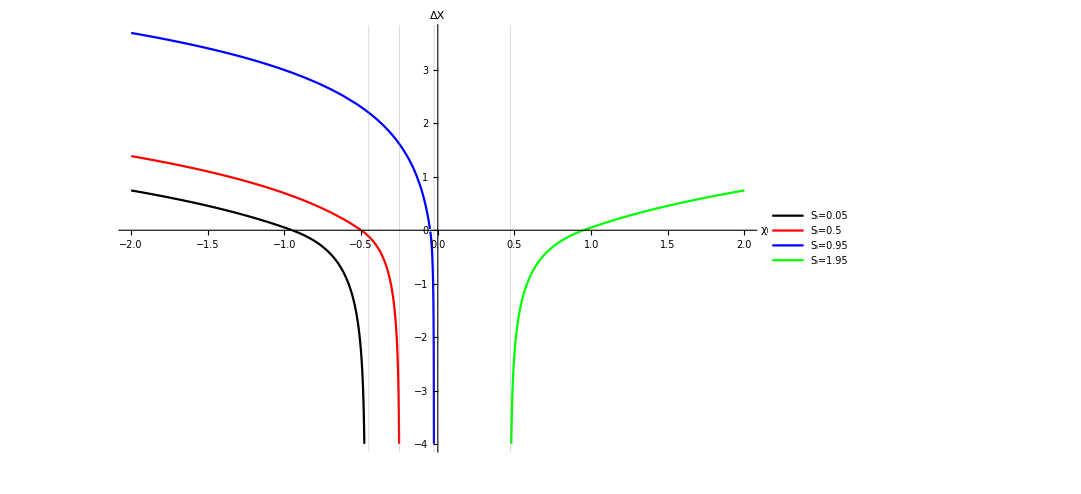

```mathematica
Plot[Evaluate[Sign[r]*Log[1-Abs[r]]/.r->(s-1)/x-1/.s->{0.05,0.5,0.95,1.95}],{x,-2,2},AxesLabel->{"χ_i","ΔX"},PlotStyle->{Black,Red,Blue,Green},LabelStyle->{20,Bold},GridLines->{{{(0.1-1)/2,{Dashed,Black,Thick}},{(0.5-1)/2,{Red, Dashed,Thick}},{(0.95-1)/2,{Blue,Dashed,Thick}},{(1.95-1)/2,{Green,Dashed,Thick}}},None},PlotLegends->Placed[{"S_i=0.05","S_i=0.5","S_i=0.95","S_i=1.95"},Scaled[{0.85,0.25}]],ImageSize->{800,600}]
```

```mathematica
Plot3D[Sign[r]*Log[1-Abs[r]]/.r->(s-1)/x-1,{x,-1.5,1.5},{s,-0.5,2.5}]
```

-Graphics3D-

```mathematica
L=100;
tabS={-1.5,-0.5,0.25,0.5,0.75,1.05};
sol1neg=Table[NDSolve[{
D[n[x,t],t]==D[n[x,t],{x,2}]-n[x,t]+UnitStep[(Sign[S]*n[x,t]-S)],
n[x,0]==1.25*UnitStep[-x],(D[n[x,t],x]/.x->-L/2)==0,(D[n[x,t],x]/.x->L/2)==0},{n},{x,-L/2,L/2},{t,0,5},AccuracyGoal->2,Method->{"PDEDiscretization"->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->2^8},"DifferentiateBoundaryConditions"->True},"TimeIntegration"->Automatic},MaxSteps->1000,MaxStepSize->Automatic,StartingStepSize->Automatic],{S,Take[tabS,2]}];
sol1pos=Table[NDSolve[{
D[n[x,t],t]==D[n[x,t],{x,2}]-n[x,t]+UnitStep[(Sign[S]*n[x,t]-S)],
n[x,0]==1.25*UnitStep[-x],(D[n[x,t],x]/.x->-L/2)==0,(D[n[x,t],x]/.x->L/2)==0},{n},{x,-L/2,L/2},{t,0,50},AccuracyGoal->3,Method->{"PDEDiscretization"->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->2^8},"DifferentiateBoundaryConditions"->True},"TimeIntegration"->Automatic},MaxSteps->Automatic,MaxStepSize->Automatic,StartingStepSize->Automatic],{S,Take[tabS,-4]}];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::mxst: Maximum number of 1000 steps reached at the point t == 2.70611.

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

```mathematica
Plot3D[n[x,t]/.sol1neg[[2]],{x,-L/2,L/2},{t,0,2.5},PlotRange->All,PlotPoints->50]
```

-Graphics3D-

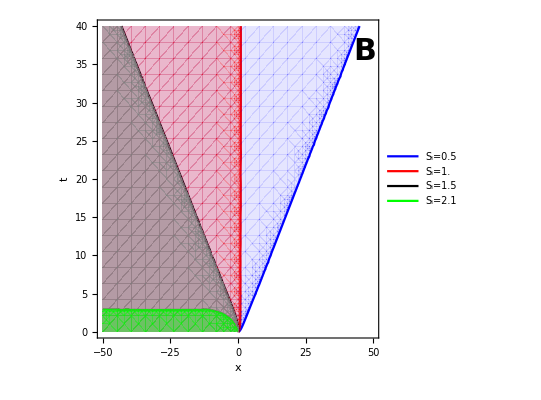

```mathematica
Show[ContourPlot[Evaluate[Table[n[x,t]==tabS[[i]]/.sol[[i]],{i,1,4}]],{x,-L/2,L/2},{t,0,40},MaxRecursion->4,PerformanceGoal->"Quality",ContourStyle->{Blue,Red,Black,Green},FrameLabel->{"x","t"},LabelStyle->{20,Bold},ImageSize->{400,400},PlotLegends->Placed[Table[StringForm["S_i=``",2*tabS[[i]]],{i,1,4}],Scaled[{0.85,0.25}]],(*Epilog->Inset[Plot[n[x,500]/.sol[[2]],{x,-L/2,L/2},AxesLabel->{"x","ψ(x,+∞)"},Ticks->{{-40,0,40},{0,1}},PlotStyle->Red,Filling->{1->Bottom},LabelStyle->{20,Bold},ImageSize->{120,100}],Scaled[{0.72,0.85}]],*)ContourLabels->None],RegionPlot[Evaluate[Table[n[x,t]>tabS[[i]]/.sol[[i]],{i,1,4}]],{x,-L/2,L/2},{t,0,40},MaxRecursion->4,PerformanceGoal->"Quality",BoundaryStyle->None,PlotStyle->{Directive[Blue,Opacity[0.1]],Directive[Red,Opacity[0.2]],Directive[Gray,Opacity[0.5]],Directive[Green,Opacity[0.4]]}],Epilog->Inset[Style["B",30,Bold],Scaled[{0.95,0.9}]]]
```

```mathematica
tab1pos=Table[Plot3D[n[x,t]/.sol1pos[[k]],{x,-L/2,L/2},{t,0,50},PlotRange->{Automatic,Automatic,{-0.1,1.25}},(*Epilog->Inset[Style[StringForm["S_i=``",2tabS[[k+2]]],20,Bold,Gray],{0.5,0.9}],*)AxesLabel->{If[k>1,None,"x"],If[k>1,None,"t"],(*"ψ(x,t)"*)None},PlotPoints->50,AxesEdge->{{1,-1},{1,-1},{1,-1}},ViewPoint->Evaluate[{r*Cos[ϕ]*Sin[θ],r*Sin[ϕ]Sin[θ],r*Cos[θ]}/.{r->3,ϕ->2π/8,θ->4π/12}],ColorFunction->"Rainbow",LabelStyle->{20,Bold},Mesh->None,Ticks->(*{Automatic,Automatic,{0,1,2}}*)None],{k,1,4}]
tab1neg=Table[Plot3D[n[x,t]/.sol1neg[[k]],{x,-L/2,L/2},{t,0,If[k==1,5,2.5]},PlotRange->{Automatic,Automatic,{-0.1,1.25}},Mesh->None,Epilog->Inset[Style[If[k==1,"C_i/ϵ_ii>OverTilde[ψ_i]","C_i/ϵ_ii<OverTilde[ψ_i]"],20,Bold,Gray],{0.5,0.9}],AxesLabel->{"x","t",(*"ψ(x,t)"*)None},PlotPoints->50,AxesEdge->{{1,-1},{1,-1},{1,-1}},ViewPoint->Evaluate[{r*Cos[ϕ]*Sin[θ],r*Sin[ϕ]Sin[θ],r*Cos[θ]}/.{r->3,ϕ->2π/8,θ->4π/12}],ColorFunction->"Rainbow",LabelStyle->{20,Bold},Ticks->(*{Automatic,Automatic,{0,1,2}}*)None],{k,1,2}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-}

```mathematica
Plot3D[n[x,t]/.sol[[1]],{x,-L/2,L/2},{t,0,4},PlotRange->{Automatic,Automatic,{-0.1,2}},Epilog->Inset[Style["H/γ<C/ϵ",20,Bold],{0.5,1.0}],AxesLabel->{"x","t",(*"ψ(x,t)"*)None},PlotPoints->50,AxesEdge->{{1,-1},{1,-1},{1,-1}},ViewPoint->Evaluate[{r*Cos[ϕ]*Sin[θ],r*Sin[ϕ]Sin[θ],r*Cos[θ]}/.{r->3,ϕ->2π/8,θ->4π/12}],ColorFunction->"Rainbow",LabelStyle->{20,Bold},Ticks->(*{Automatic,Automatic,{0,1,2}}*)None,ImageSize->{400,300},ImagePadding->{{Automatic,Automatic},{Automatic,50}}]
Plot3D[n[x,t]/.sol[[2]],{x,-L/2,L/2},{t,0,4},PlotRange->{Automatic,Automatic,{-0.1,2}},Epilog->Inset[Style["H/γ>C/ϵ",20,Bold],{0.5,1.0}],AxesLabel->{"x","t",(*"ψ(x,t)"*)None},PlotPoints->50,AxesEdge->{{1,-1},{1,-1},{1,-1}},ViewPoint->Evaluate[{r*Cos[ϕ]*Sin[θ],r*Sin[ϕ]Sin[θ],r*Cos[θ]}/.{r->3,ϕ->2π/8,θ->4π/12}],ColorFunction->"Rainbow",LabelStyle->{20,Bold},Ticks->(*{Automatic,Automatic,{0,1,2}}*)None,ImageSize->{400,300},ImagePadding->{{Automatic,Automatic},{Automatic,50}}]
```

-Graphics3D-

-Graphics3D-

```mathematica
plotV1d=GraphicsRow[{Plot[-(S-1)/Sqrt[(1-(S-1)^2)],{S,0,2},FrameLabel->{"S_i","v_i(4D_iγ_i)^(-1/2)"},PlotRange->{{0,2.75},{-7,7}},LabelStyle->{20,Bold},PlotStyle->{Thick,Blue},GridLines->{{1,2},{}},GridLinesStyle->Directive[{Dashed,Thick,Black}],PlotRangeClipping->False,Frame->True,AspectRatio->0.5,Epilog->{
(*Inset[Graphics[{Dashed,Line[{{0,0},{0,2}}]}],{1.0,4}],*)
Inset[Style["expanding\ndomain",Bold,20,Gray],{0.6,4}],Inset[Style["shrinking\ndomain",Bold,20,Gray],{1.5,4}],Inset[Style["collapsing\ndomain",Bold,20,Gray],{2.4,4}],(*Inset[Style["C",30,Bold],Scaled[{1,1.03}]],*)Inset[Style["B",30,Bold],Scaled[{0.05,0.9}]],Inset[Style["C_i>0",30,Bold,Gray],Scaled[{0.5,1.07}]],
Inset[tab1pos[[1]],{0.35,-3},Automatic,{6.5,6.5}],Inset[tab1pos[[2]],{1.0,-3},Automatic,{6.5,6.5}],Inset[tab1pos[[3]],{1.65,-3},Automatic,{6.5,6.5}],Inset[tab1pos[[4]],{2.4,-3},Automatic,{6.5,6.5}],Inset[tab1neg[[1]],{3.23,-4},Automatic,{6.5,6.5}],Inset[tab1neg[[2]],{3.23,2},Automatic,{6.5,6.5}],Inset[Style["C_i<0",30,Bold,Gray],Scaled[{1.15,1.07}]],Inset[Style["C",30,Bold,Black],Scaled[{1.05,0.9}]](*,
Arrow[{{0.5,-7},{0.33,-5}}],Arrow[{{1.0,-7},{1.0,-5}}],Arrow[{{1.5,-7},{1.67,-5}}],Arrow[{{2.1,-7},{2.4,-5}}]*)},ImagePadding->{{60,145},{Automatic,30}}](*,Plot[,{x,-1,1},AspectRatio->2]*)},ImageSize->{750,Automatic},ImagePadding->{{0,0},{0,0}}]
(*Plot[,{x,-1,1},Axes->False,Epilog->Inset[plotV1d],ImageSize->{900,Automatic}]*)
```

-Graphics-

General::munfl: Exp[-6355.56] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6403.29] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-57610.3] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

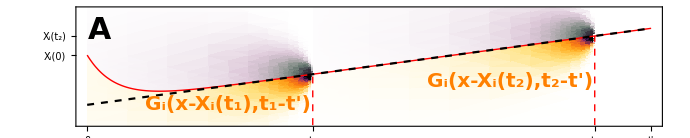

```mathematica
G[x_,t_]:=Exp[-0.55t-x^2/t/0.2]/Sqrt[2π*t];
X[t_]:=Exp[-2t](0.65)+0.1*t-0.5;
t1=4;t2=9;
int1plot=Show[
DensityPlot[G[x-X[t1],t1-t],{t,0,10},{x,-1,1},FrameLabel->None,LabelStyle->{20,Bold},FrameTicks->{{{{X[0],"X_i(0)"},{X[t1],"X_i(t_1)"},{X[t2],"X_i(t_2)"},{0.749,"x"}},None},{{0,{t1,"t_1"},{t2,"t_2"},{9.99,"t'"}},None}},PlotRange->{All,{-1,0.75},{0,2.0}},PlotRangePadding->None,
RegionFunction->Function[{x,y,z},x<t1&&y<X[x]],ColorFunction->Function[{z},If[z<0.5,ColorData[{"SunsetColors","Reverse"}][z/0.5],ColorData[{"SunsetColors","Reverse"}][1]]],
PlotLegends->Placed[LineLegend[{Red,{Black,Dashed}},{Style["X_i(t')",Red],"v_it'+(X̃)_i"}],{0.2,0.7}],PlotRangeClipping->True,
Epilog->{
{Red,Thick,Dashed,Line[{{t1,-1},{t1,X[t1]}}]},{Red,Thick,Dashed,Line[{{t2,-1},{t2,X[t2]}}]},
Inset[Style["G_i(x-X_i(t_1),t_1-t')",20,Bold,Orange],{2.5,-0.5}],Inset[Style["G_i(x-X_i(t_2),t_2-t')",20,Bold,Orange],{7.5,-0.2}],Inset[Style["A",Bold,30],Scaled[{0.04,0.8}]]}
],
DensityPlot[G[x-X[t2],t2-t],{t,0,10},{x,-1,1},PlotRange->{All,All,{0,2}},
RegionFunction->Function[{x,y,z},t1<x<t2&&y<X[x]],
ColorFunction->Function[{z},If[z<0.5,ColorData[{"SunsetColors","Reverse"}][z/0.5],ColorData[{"SunsetColors","Reverse"}][1]]]],
DensityPlot[G[x-X[t2],t2-t],{t,0,10},{x,-1.,1},PlotRange->{All,All,{0,2}},
RegionFunction->Function[{x,y,z},t1<x&&1>y>X[x]],
ColorFunction->Function[{z},If[z<0.5,ColorData[{"PigeonTones","Reverse"}][z/0.5],ColorData[{"PigeonTones","Reverse"}][1]]]],
DensityPlot[G[x-X[t1],t1-t],{t,0,10},{x,-1.,1},PlotRange->{All,All,{0,2}},
RegionFunction->Function[{x,y,z},x<t1&&1>y>X[x]],
ColorFunction->Function[{z},If[z<0.5,ColorData[{"PigeonTones","Reverse"}][z/0.5],ColorData[{"PigeonTones","Reverse"}][1]]]],
Plot[{X[t],0.1t-0.5},{t,0,10},PlotStyle->{{Red,Thick},{Black,Dashed}}],PlotRange->{Automatic,{-0.75,0.75}},ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}},AspectRatio->0.2,ImageSize->{690,Automatic}]
```

```mathematica
GraphicsColumn[{int1plot,plotV1d},ImageSize->{750,Automatic},Spacings->{-20,-9},ImagePadding->{{Automatic,Automatic},{0,0}}]
```

-Graphics-

```mathematica
G1[x_,t_]:=Exp[-2.5t-x^2/t/4.2]/Sqrt[2π*t];
G2[x_,t_]:=Exp[-1.5t-x^2/t/1]/Sqrt[2π*t];
X1[t_]:=Exp[-2t](-0.5)+0.1*t-0.5;
X2[t_]:=X1[t]+2Exp[-5t]+0.3;
t0=4;
GraphicsGrid[{{
Show[
DensityPlot[G1[x-X1[t0],t0-t],{t,0,5},{x,-1.5,1.5},PlotRange->{{0,5},{-1.5,1.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&y<X1[x]],ColorFunction->Function[{z},If[z<0.3,Blend[{White,Blue,RGBColor[0,0,0.5]},z/0.3],RGBColor[0,0,0.5]]],
FrameLabel->{None,"x"},
FrameTicks->{{None,None},{None,None}},LabelStyle->{20,Bold},
Epilog->{{Dashed,Blue,Line[{{t0,-1.5},{t0,X1[t0]}}]},Inset[Style["G_1(x-X_1(t_0),t_0-t)",Blue,Bold,15],{2.5,-0.75}],Inset[LineLegend[{Blue,Red},{Style["X_1(t)",20,Bold],Style["X_2(t)",20,Bold]}],Scaled[{0.25,0.75}]]},
ImageSize->{400,400},AspectRatio->1/2
],
DensityPlot[G1[x-X1[t0],t0-t],{t,0,5},{x,-1.5,1.5},PlotRange->{{0,5},{-1.5,1.5},{0,2}},RegionFunction->Function[{x,y,z},X1[x]<y],ColorFunction->Function[{z},If[z<0.3,Blend[{White,RGBColor[0.2,0.2,0.2],Black},z/0.3],Black]]
],
Plot[{X1[t],X2[t]},{t,0,5},PlotStyle->{Blue,Red}]
],
Show[
DensityPlot[G2[x-X1[t0],t0-t],{t,0,5},{x,-1.5,1.5},PlotRange->{{0,5},{-1.5,1.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&y>X1[x]],ColorFunction->Function[{z},If[z<0.3,Blend[{White,Blue,RGBColor[0,0,0.5]},z/0.3],RGBColor[0,0,0.5]]],FrameTicks->{{None,{{X1[t0],"X_1(t_0)"},{X2[t0],"X_2(t_0)"}}},{None,None}},LabelStyle->{20,Bold},
Epilog->{{Dashed,Blue,Line[{{t0,X2[t0]},{t0,1.5}}]},Inset[Style["G_2(x-X_1(t_0),t_0-t)",Blue,Bold,15],{2.75,0.65}]},
ImageSize->{400,400},AspectRatio->1/2
],
DensityPlot[G2[x-X1[t0],t0-t],{t,0,5},{x,-1.5,1.5},PlotRange->{{0,5},{-1.5,1.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&X2[x]>y],ColorFunction->Function[{z},If[z<0.3,Blend[{White,RGBColor[0.2,0.2,0.2],Black},z/0.3],Black]]
],
Plot[{X1[t],X2[t]},{t,0,5},PlotStyle->{Blue,Red}]
]
},{
Show[
DensityPlot[G1[x-X2[t0],t0-t],{t,0,5},{x,-1.5,1.5},PlotRange->{{0,5},{-1.5,1.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&y<=X1[x]],ColorFunction->Function[{z},If[z<0.3,Blend[{White,Red,RGBColor[0.5,0,0]},z/0.3],RGBColor[0.5,0,0]]],
FrameLabel->{"t","x"},
FrameTicks->{{None,None},{{0,{t0,"t_0"}},None}},LabelStyle->{20,Bold},
Epilog->{{Dashed,Red,Line[{{t0,X1[t0]},{t0,-1.5}}]},Inset[Style["G_1(x-X_2(t_0),t_0-t)",Red,Bold,15],{2.5,-0.65}]},
ImageSize->{400,400},AspectRatio->1/2
],
DensityPlot[G1[x-X2[t0],t0-t],{t,0,5},{x,-1.5,1.5},PlotRange->{{0,5},{-1.5,1.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&X1[x]<y],ColorFunction->Function[{z},If[z<0.3,Blend[{White,RGBColor[0.2,0.2,0.2],Black},z/0.3],Black]]
],
Plot[{X1[t],X2[t]},{t,0,5},PlotStyle->{Blue,Red}]
],
Show[
DensityPlot[G2[x-X2[t0],t0-t],{t,0,5},{x,-1.5,1.5},PlotRange->{{0,5},{-1.5,1.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&y>X2[x]],ColorFunction->Function[{z},If[z<0.3,Blend[{White,Red,RGBColor[0.5,0,0]},z/0.3],RGBColor[0.5,0,0]]],
FrameLabel->{"t",None},
FrameTicks->{{None,{{X1[t0],"X_1(t_0)"},{X2[t0],"X_2(t_0)"}}},{{0,{t0,"t_0"}},None}},LabelStyle->{20,Bold},
Epilog->{{Dashed,Red,Line[{{t0,X2[t0]},{t0,1.5}}]},Inset[Style["G_2(x-X_2(t_0),t_0-t)",Red,Bold,15],{2.5,0.65}]},
ImageSize->{400,400},AspectRatio->1/2
],
DensityPlot[G2[x-X2[t0],t0-t],{t,0,5},{x,-1.5,1.5},PlotRange->{{0,5},{-1.5,1.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&X2[x]>y],ColorFunction->Function[{z},If[z<0.3,Blend[{White,RGBColor[0.2,0.2,0.2],Black},z/0.3],Black]]
],
Plot[{X1[t],X2[t]},{t,0,5},PlotStyle->{Blue,Red}]
]
}},ImageSize->{850,500},Spacings->{-70,-230},ImagePadding->{{Automatic,Automatic},{150,150}}]
```

-Graphics-

```mathematica
G1[x_,t_]:=Exp[-2.5t-x^2/t/4.2]/Sqrt[2π*t];
G2[x_,t_]:=Exp[-1.5t-x^2/t/1]/Sqrt[2π*t];
X1[t_]:=Exp[-2t](-0.5)+0.75*t-0.5;
X2[t_]:=-0.5t+2Exp[-5t]+0.2;
t0=4;
GraphicsGrid[{{
Show[
DensityPlot[G2[x-X2[t0],t0-t]+G1[x-X1[t0],t0-t],{t,0,5},{x,-2.5,3.5},PlotRange->{{0,5},{-2.5,3.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&y<X1[x]],ColorFunction->Function[{z},If[z<0.3,Blend[{White,Blue,RGBColor[0.0,0,0.5]},z/0.3],RGBColor[0.0,0,0.5]]],
FrameLabel->{"t","x"},
FrameTicks->{{None,(*{{X1[t0],"X_1(t_0)"},{X2[t0],"X_2(t_0)"}}*)None},{{0,{t0,"t_0"}},None}},LabelStyle->{20,Bold},
Epilog->{{Dashed,Blue,Line[{{t0,X1[t0]},{t0,-2.5}}]},Inset[Style["G_2(x-X_2(t_0),t_0-t)",Red,Bold,15],{2.5,-1.9}],Inset[Style["G_1(x-X_1(t_0),t_0-t)",Blue,Bold,15],{2.5,2.75}]},
(*ImageSize->{400,400},*)AspectRatio->1/2
],
DensityPlot[G2[x-X2[t0],t0-t]+G1[x-X1[t0],t0-t],{t,0,5},{x,-2.5,3.5},PlotRange->{{0,5},{-1.5,3.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&X1[x]<y],ColorFunction->Function[{z},If[z<0.3,Blend[{White,RGBColor[0.2,0.2,0.2],Black},z/0.3],Black]]
],
Plot[{X1[t],X2[t]},{t,0,5},PlotStyle->{Blue,Red}]
],
Show[
DensityPlot[G2[x-X2[t0],t0-t]+G1[x-X1[t0],t0-t],{t,0,5},{x,-2.5,3.5},PlotRange->{{0,5},{-2.5,3.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&y>X2[x]],ColorFunction->Function[{z},If[z<0.3,Blend[{White,Red,RGBColor[0.5,0,0]},z/0.3],RGBColor[0.5,0,0]]],
FrameLabel->{"t",None},
FrameTicks->{{None,{{X1[t0],"X_1(t_0)"},{X2[t0],"X_2(t_0)"}}},{{0,{t0,"t_0"}},None}},LabelStyle->{20,Bold},
Epilog->{{Dashed,Red,Line[{{t0,X2[t0]},{t0,3.5}}]},Inset[Style["G_2(x-X_2(t_0),t_0-t)",Red,Bold,15],{2.5,-1.9}],Inset[Style["G_1(x-X_1(t_0),t_0-t)",Blue,Bold,15],{2.5,2.75}]},
(*ImageSize->{400,400},*)AspectRatio->1/2
],
DensityPlot[G2[x-X2[t0],t0-t]+G1[x-X1[t0],t0-t],{t,0,5},{x,-2.5,1.5},PlotRange->{{0,5},{-1.5,1.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&X2[x]>y],ColorFunction->Function[{z},If[z<0.3,Blend[{White,RGBColor[0.2,0.2,0.2],Black},z/0.3],Black]]
],
Plot[{X1[t],X2[t]},{t,0,5},PlotStyle->{Blue,Red}]]
}},ImageSize->{750,250},Spacings->{-50,Automatic},ImagePadding->{{175,190},{Automatic,Automatic}}]
```

General::munfl: Exp[-1358.03] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1375.97] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.83095×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
G1[x_,t_]:=Exp[-2.5t-x^2/t/4.2]/Sqrt[2π*t];
G2[x_,t_]:=Exp[-1.5t-x^2/t/1]/Sqrt[2π*t];
X1[t_]:=Exp[-3t](-0.4)-0.25*t-0.4;
X2[t_]:=0.4t+Exp[-4t]+1.0;
t0=4;
GraphicsGrid[{{
Show[
DensityPlot[G2[x-X2[t0],t0-t]+G1[x-X1[t0],t0-t],{t,0,5},{x,-2.5,3.5},PlotRange->{{0,5},{-2.5,3.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&y<X1[x]],ColorFunction->Function[{z},If[z<0.3,Blend[{White,Blue,RGBColor[0.0,0,0.5]},z/0.3],RGBColor[0.0,0,0.5]]],
FrameLabel->{"t","x"},
FrameTicks->{{None,(*{{X1[t0],"X_1(t_0)"},{X2[t0],"X_2(t_0)"}}*)None},{{0,{t0,"t_0"}},None}},LabelStyle->{20,Bold},
Epilog->{{Dashed,Blue,Line[{{t0,X1[t0]},{t0,-2.5}}]},Inset[Style["G_2(x-X_2(t_0),t_0-t)",Red,Bold,15],{2.5,2.75}],Inset[Style["G_1(x-X_1(t_0),t_0-t)",Blue,Bold,15],{2.5,-1.9}]},
(*ImageSize->{400,400},*)AspectRatio->1/2
],
DensityPlot[G2[x-X2[t0],t0-t]+G1[x-X1[t0],t0-t],{t,0,5},{x,-2.5,3.5},PlotRange->{{0,5},{-1.5,3.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&X1[x]<y],ColorFunction->Function[{z},If[z<0.3,Blend[{White,RGBColor[0.2,0.2,0.2],Black},z/0.3],Black]]
],
Plot[{X1[t],X2[t]},{t,0,5},PlotStyle->{Blue,Red}]
],
Show[
DensityPlot[G2[x-X2[t0],t0-t]+G1[x-X1[t0],t0-t],{t,0,5},{x,-2.5,3.5},PlotRange->{{0,5},{-2.5,3.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&y>X2[x]],ColorFunction->Function[{z},If[z<0.3,Blend[{White,Red,RGBColor[0.5,0,0]},z/0.3],RGBColor[0.5,0,0]]],
FrameLabel->{"t",None},
FrameTicks->{{None,{{X1[t0],"X_1(t_0)"},{X2[t0],"X_2(t_0)"}}},{{0,{t0,"t_0"}},None}},LabelStyle->{20,Bold},
Epilog->{{Dashed,Red,Line[{{t0,X2[t0]},{t0,3.5}}]},Inset[Style["G_2(x-X_2(t_0),t_0-t)",Red,Bold,15],{2.5,2.75}],Inset[Style["G_1(x-X_1(t_0),t_0-t)",Blue,Bold,15],{2.5,-1.9}]},
(*ImageSize->{400,400},*)AspectRatio->1/2
],
DensityPlot[G2[x-X2[t0],t0-t]+G1[x-X1[t0],t0-t],{t,0,5},{x,-2.5,3.5},PlotRange->{{0,5},{-1.5,3.5},{0,2}},RegionFunction->Function[{x,y,z},x<t0&&X2[x]>y],ColorFunction->Function[{z},If[z<0.3,Blend[{White,RGBColor[0.2,0.2,0.2],Black},z/0.3],Black]]
],
Plot[{X1[t],X2[t]},{t,0,5},PlotStyle->{Blue,Red}]]
}},ImageSize->{750,250},Spacings->{-50,Automatic},ImagePadding->{{175,190},{Automatic,Automatic}}]
```

General::munfl: Exp[-1189.31] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4.1756×10^6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1205.33] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

```mathematica
tmax=36000;
L=500;
(*non-stable, overlapping*)
ϵ11=1.0;ϵ22=1.0;ϵ12=-0.2;ϵ21=-1.0;d1=1;d2=1;γ1=0.0005;γ2=0.0004;h1=0.01;h2=0.02;c1=3.5;c2=6.0;x1=-3L/8;x2=3L/8;
S1=2c1*γ1/h1/ϵ11
S2=2c2*γ2/h2/ϵ22
sol2=NDSolve[{
D[n1[x,t],t]==d1*D[n1[x,t],{x,2}]-γ1*n1[x,t]+h1*UnitStep[ϵ11*n1[x,t]+ϵ12*n2[x,t]-c1],
D[n2[x,t],t]==d2*D[n2[x,t],{x,2}]-γ2*n2[x,t]+h2*UnitStep[ϵ22*n2[x,t]+ϵ21*n1[x,t]-c2],
n1[x,0]==1.1c1/ϵ11*UnitStep[x1-x],n2[x,0]==1.1c2/ϵ22*UnitStep[x-x2],(D[n1[x,t],x]/.x->-L/2)==0,(D[n1[x,t],x]/.x->L/2)==0,(D[n2[x,t],x]/.x->-L/2)==0,(D[n2[x,t],x]/.x->L/2)==0},{n1,n2},{x,-L/2,L/2},{t,0,tmax},AccuracyGoal->3, Method->{"PDEDiscretization"->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->2^11},"DifferentiateBoundaryConditions"->True},"TimeIntegration"->"BDF"},MaxStepSize->Automatic,StartingStepSize->Automatic];
Plot3D[Evaluate[{n1[x,t],n2[x,t]}/.sol2],{x,-L/2,L/2},{t,0,tmax},PlotRange->All]
v1=Sqrt[4d1*γ1]*Abs[S1-1]/Sqrt[1-(S1-1)^2];
v2=Sqrt[4d2*γ2]*Abs[S2-1]/Sqrt[1-(S2-1)^2];
T0=(x2-x1)/(Abs[v2]+Abs[v1]);
If[S1>1,v1=-v1];
If[S2<1,v2=-v2];
If[v1>0&&v2<0,X0=(Abs[v1]*x2+Abs[v2]*x1)/(Abs[v1]+Abs[v2])];
(*ContourPlot[{c1==ϵ11*h1/2/γ1*(-v/Sqrt[4d1*γ1+v^2]+1)+ϵ12*h2/2/γ2*(1-Sign[Δc]+Exp[v*Δc/4/d2-Abs[Δc]*Sqrt[4d2*γ2+v^2]/2/d2]*(v/Sqrt[4d2*γ2+v^2]+Sign[Δc])),c2==ϵ21*h1/2/γ1*(1-Sign[Δc]-Exp[-v*Δc/4/d1-Abs[Δc]*Sqrt[4d1*γ1+v^2]/2/d1]*(v/Sqrt[4d1*γ1+v^2]-Sign[Δc]))+ϵ22*h2/2/γ2*(v/Sqrt[4d2*γ2+v^2]+1)},{v,-200,200},{Δc,-200,200},FrameLabel->{"v","Δc"}]*)
solV=FindRoot[{c1==ϵ11*h1/2/γ1*(-v/Sqrt[4d1*γ1+v^2]+1)+ϵ12*h2/2/γ2*(1-Sign[Δc]+Exp[v*Δc/4/d2-Abs[Δc]*Sqrt[4d2*γ2+v^2]/2/d2]*(v/Sqrt[4d2*γ2+v^2]+Sign[Δc])),c2==ϵ21*h1/2/γ1*(1-Sign[Δc]-Exp[-v*Δc/4/d1-Abs[Δc]*Sqrt[4d1*γ1+v^2]/2/d1]*(v/Sqrt[4d1*γ1+v^2]-Sign[Δc]))+ϵ22*h2/2/γ2*(v/Sqrt[4d2*γ2+v^2]+1)},{{v,0(*RandomReal[{-0.5,0.5}]*)},{Δc,(*RandomReal[{-0.5,0.5}]*)-20}}]
empX1=FindRoot[ϵ11*n1[x1,tmax]+ϵ12*n2[x1,tmax]==c1/.sol2,{x1,X0},AccuracyGoal->3][[1,2]];
empX2=FindRoot[ϵ21*n1[x2,tmax]+ϵ22*n2[x2,tmax]==c2/.sol2,{x2,X0},AccuracyGoal->3][[1,2]];
center=(empX2+empX1)/2;
```

0.35

0.24

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

-Graphics3D-

{v→-0.00412787,Δc→-39.793}

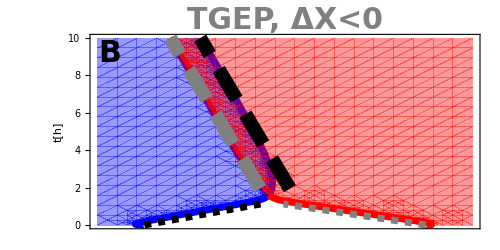

```mathematica
plotTGEP1=Show[{ContourPlot[Evaluate[{ϵ11*n1[x,t]+ϵ12*n2[x,t]==c1/.sol2,ϵ21*n1[x,t]+ϵ22*n2[x,t]==c2/.sol2}/.t->3600*τ],{x,-L/2,L/2},{τ,0,tmax/3600},ContourStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}},LabelStyle->{Bold,30},ContourLabels->None,FrameLabel->{None(*Style["x[μm]",Opacity[0]]*),"t[h]"},FrameTicks->{{Automatic,None},{(*Table[{i,Style["a",Opacity[0]]},{i,-250,250,20}]*)None,None}},PlotRangeClipping->False,ImagePadding->{{Automatic,Automatic},{Automatic,50}},MaxRecursion->5,PerformanceGoal->"Quality",AspectRatio->1/2,Epilog->{
(*Inset[LineLegend[{Directive[{Blue,Thickness[0.01]}],Directive[{Red,Thickness[0.01]}],Directive[{Black,Dashed,Thickness[0.01]}],Directive[{Gray,Dashed,Thickness[0.01]}],Directive[{Black,Dashing[{0.05,0.025}],Thickness[0.02]}],Directive[{Gray,Dashing[{0.05,0.025}],Thickness[0.02]}]},{Style["X_1(t)",30,Bold],Style["X_2(t)",30,Bold],Style["X_1(0)+v_1t",30,Bold],Style["X_2(0)+v_2t",30,Bold],Style["vt-ΔX/2+c_0",30,Bold],Style["vt+ΔX/2+c_0",30,Bold]},LegendLayout->{"Column",2}],Scaled[{0.5,0.5}]],*)
Inset[Style["B",30,Bold],Scaled[{0.05,.9}]],Inset[Style["TGEP, ΔX<0",Bold,30,Gray],Scaled[{0.5,1.07}]]}
],
RegionPlot[Evaluate[{ϵ11*n1[x,t]+ϵ12*n2[x,t]>c1/.sol2,ϵ21*n1[x,t]+ϵ22*n2[x,t]>c2/.sol2}/.t->3600*τ],{x,-L/2,L/2},{τ,0,tmax/3600},BoundaryStyle->None,PlotStyle->{Directive[Blue,Opacity[0.4]],Directive[Red,Opacity[0.4]]},MaxRecursion->5,PerformanceGoal->"Quality"],ParametricPlot[Evaluate[{{HeavisideTheta[T0/3600-t]*(x1+v1*3600*t)+HeavisideTheta[t-T0/3600]*(center+v*(3600*t-tmax)-Δc/2),t},{HeavisideTheta[T0/3600-t]*(x2+v2*3600*t)+HeavisideTheta[t-T0/3600]*(center+v*(3600*t-tmax)+Δc/2),t}}/.solV],{t,0,T0/3600-0.1},(*RegionFunction->Function[{x,y,u,v},!((T0-100)<u)],*)PlotStyle->{{Black,Thickness[0.01],Dashed},{Gray,Thickness[0.01],Dashed}}],
ParametricPlot[Evaluate[{{center+v*(3600*t-tmax)-Δc/2,t},{center+v*(3600*t-tmax)+Δc/2,t}}/.solV],{t,7000/3600,tmax/3600},(*,PlotRange->{Automatic,{0,tmax}},*)PlotStyle->{{Black,Thickness[0.02],Dashing[{0.05,0.025}]},{Gray,Thickness[0.02],Dashing[{0.05,0.025}]}}]},ImageSize->{500,250}]
```

```mathematica
legend=Plot[,{x,-L/2,L/2},Axes->False,PlotRangeClipping->False,Epilog->Inset[LineLegend[{Directive[{Blue,Thickness[0.01]}],Directive[{Red,Thickness[0.01]}],Directive[{Black,Dashed,Thickness[0.01]}],Directive[{Gray,Dashed,Thickness[0.01]}],Directive[{Black,Dashing[{0.05,0.025}],Thickness[0.02]}],Directive[{Gray,Dashing[{0.05,0.025}],Thickness[0.02]}]},{Style["X_1(t)",30,Bold],Style["X_2(t)",30,Bold],Style["X_1(0)+v_1t",30,Bold],Style["X_2(0)+v_2t",30,Bold],Style["vt-ΔX/2+c_0",30,Bold],Style["vt+ΔX/2+c_0",30,Bold]},LegendLayout->{"Column",2}],Scaled[{0.5,0.5}]],ImageSize->{500,250}]
```

-Graphics-

```mathematica
tmax=36000;
L=500;
(*non-stable, depleted zone*)
ϵ11=1.0;ϵ22=1.0;ϵ12=-0.45;ϵ21=-2.1;d1=1;d2=1;γ1=0.0005;γ2=0.0004;h1=0.01;h2=0.02;c1=4.0;c2=6.5;
S1=2c1*γ1/h1/ϵ11
S2=2c2*γ2/h2/ϵ22
sol2=NDSolve[{
D[n1[x,t],t]==d1*D[n1[x,t],{x,2}]-γ1*n1[x,t]+h1*UnitStep[ϵ11*n1[x,t]+ϵ12*n2[x,t]-c1],
D[n2[x,t],t]==d2*D[n2[x,t],{x,2}]-γ2*n2[x,t]+h2*UnitStep[ϵ22*n2[x,t]+ϵ21*n1[x,t]-c2],
n1[x,0]==1.1c1/ϵ11*UnitStep[x1-x],n2[x,0]==1.1c2/ϵ22*UnitStep[x-x2],(D[n1[x,t],x]/.x->-L/2)==0,(D[n1[x,t],x]/.x->L/2)==0,(D[n2[x,t],x]/.x->-L/2)==0,(D[n2[x,t],x]/.x->L/2)==0},{n1,n2},{x,-L/2,L/2},{t,0,tmax},AccuracyGoal->3, Method->{"PDEDiscretization"->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->2^11},"DifferentiateBoundaryConditions"->True},"TimeIntegration"->"BDF"},MaxStepSize->Automatic,StartingStepSize->Automatic];
Plot3D[Evaluate[{n1[x,t],n2[x,t]}/.sol2],{x,-L/2,L/2},{t,0,tmax},PlotRange->All]
v1=Sqrt[4d1*γ1]*Abs[S1-1]/Sqrt[1-(S1-1)^2];
v2=Sqrt[4d2*γ2]*Abs[S2-1]/Sqrt[1-(S2-1)^2];
T0=(x2-x1)/(Abs[v2]+Abs[v1]);
If[S1>1,v1=-v1];
If[S2<1,v2=-v2];
If[v1>0&&v2<0,X0=(Abs[v1]*x2+Abs[v2]*x1)/(Abs[v1]+Abs[v2])];
solV=FindRoot[{c1==ϵ11*h1/2/γ1*(-v/Sqrt[4d1*γ1+v^2]+1)+ϵ12*h2/2/γ2*(1-Sign[Δc]+Exp[v*Δc/4/d2-Abs[Δc]*Sqrt[4d2*γ2+v^2]/2/d2]*(v/Sqrt[4d2*γ2+v^2]+Sign[Δc])),c2==ϵ21*h1/2/γ1*(1-Sign[Δc]-Exp[-v*Δc/4/d1-Abs[Δc]*Sqrt[4d1*γ1+v^2]/2/d1]*(v/Sqrt[4d1*γ1+v^2]-Sign[Δc]))+ϵ22*h2/2/γ2*(v/Sqrt[4d2*γ2+v^2]+1)},{{v,0(*RandomReal[{-0.5,0.5}]*)},{Δc,(*RandomReal[{-0.5,0.5}]*)-20}}]
empX1=FindRoot[ϵ11*n1[x1,tmax]+ϵ12*n2[x1,tmax]==c1/.sol2,{x1,-200},AccuracyGoal->3][[1,2]];
empX2=FindRoot[ϵ21*n1[x2,tmax]+ϵ22*n2[x2,tmax]==c2/.sol2,{x2,-200},AccuracyGoal->3][[1,2]];
center=(empX2+empX1)/2;
```

0.4

0.26

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

-Graphics3D-

{v→-0.00427539,Δc→17.421}

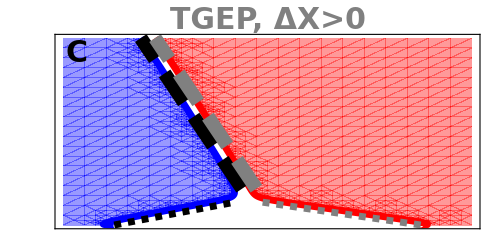

```mathematica
plotTGEP2=Show[{ContourPlot[Evaluate[{ϵ11*n1[x,t]+ϵ12*n2[x,t]==c1/.sol2,ϵ21*n1[x,t]+ϵ22*n2[x,t]==c2/.sol2}/.t->3600*τ],{x,-L/2,L/2},{τ,0,tmax/3600},ContourStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}},ContourLabels->None,LabelStyle->{30,Bold},FrameLabel->{(*"x[μm]"*)None,None(*,"t[h]"*)},FrameTicks->{{(*Table[{i,Style["a",Opacity[0]]},{i,0,10,0.5}]*)None,None},{None,None}},PlotRangeClipping->False,ImagePadding->{{Automatic,Automatic},{Automatic,50}},MaxRecursion->5,PerformanceGoal->"Quality",AspectRatio->1/2,Epilog->{
(*Inset[LineLegend[{Directive[{Blue,Thickness[0.01]}],Directive[{Red,Thickness[0.01]}],Directive[{Black,Dashed,Thickness[0.01]}],Directive[{Gray,Dashed,Thickness[0.01]}],Directive[{Black,Dashing[{0.05,0.025}],Thickness[0.02]}],Directive[{Gray,Dashing[{0.05,0.025}],Thickness[0.02]}]},{Style["X_1(t)",20,Bold],Style["X_2(t)",20,Bold],Style["X_1(0)+v_1t",20,Bold],Style["X_2(0)+v_2t",20,Bold],Style["vt-ΔX/2+c_0",20,Bold],Style["vt+ΔX/2+c_0",20,Bold]}],Scaled[{0.75,0.75}]],*)
Inset[Style["C",30,Bold],Scaled[{0.05,.9}]],Inset[Style["TGEP, ΔX>0",30,Bold,Gray],Scaled[{0.5,1.07}]]}
],
RegionPlot[Evaluate[{ϵ11*n1[x,t]+ϵ12*n2[x,t]>c1/.sol2,ϵ21*n1[x,t]+ϵ22*n2[x,t]>c2/.sol2}/.t->3600*τ],{x,-L/2,L/2},{τ,0,tmax/3600},BoundaryStyle->None,PlotStyle->{Directive[Blue,Opacity[0.4]],Directive[Red,Opacity[0.4]]},MaxRecursion->5,PerformanceGoal->"Quality"],ParametricPlot[Evaluate[{{HeavisideTheta[T0/3600-t]*(x1+v1*3600*t)+HeavisideTheta[t-T0/3600]*(center+v*(3600*t-tmax)-Δc/2),t},{HeavisideTheta[T0/3600-t]*(x2+v2*3600*t)+HeavisideTheta[t-T0/3600]*(center+v*(3600*t-tmax)+Δc/2),t}}/.solV],{t,0,T0/3600-0.1},(*RegionFunction->Function[{x,y,u,v},!((T0-100)<u)],*)PlotStyle->{{Black,Thickness[0.01],Dashed},{Gray,Thickness[0.01],Dashed}}],
ParametricPlot[Evaluate[{{center+v*(3600*t-tmax)-Δc/2,t},{center+v*(3600*t-tmax)+Δc/2,t}}/.solV],{t,7000/3600,tmax/3600},(*,PlotRange->{Automatic,{0,tmax}},*)PlotStyle->{{Black,Thickness[0.02],Dashing[{0.05,0.025}]},{Gray,Thickness[0.02],Dashing[{0.05,0.025}]}}]},ImageSize->{500,250}]
```

```mathematica
tmax=36000;
L=500;
(*exemplary params for non-stable dynamics*)
ϵ11=1.0;ϵ22=1.0;d1=1;d2=1;γ1=0.0005;γ2=0.0004;h1=0.01;h2=0.02;c1=4.5;c2=7.5;
λ1=Sqrt[d1/γ1]
λ2=Sqrt[d2/γ2]
S1=2c1*γ1/h1/ϵ11
S2=2c2*γ2/h2/ϵ22
R1=0.5;
ϵ12=(2c1-ϵ11*h1/γ1)/(R1+1)/(h2/γ2)
R2=Sign[R1]*Abs[1-(1-Abs[R1])^(λ2/λ1)]
ϵ21=(2c2-ϵ22*h2/γ2)/(R2+1)/(h1/γ1)
Sign[R1]*λ2*Log[1-Abs[R1]]
sol2=NDSolve[{
D[n1[x,t],t]==d1*D[n1[x,t],{x,2}]-γ1*n1[x,t]+h1*UnitStep[ϵ11*n1[x,t]+ϵ12*n2[x,t]-c1],
D[n2[x,t],t]==d2*D[n2[x,t],{x,2}]-γ2*n2[x,t]+h2*UnitStep[ϵ22*n2[x,t]+ϵ21*n1[x,t]-c2],
n1[x,0]==1.1c1/ϵ11*UnitStep[x1-x],n2[x,0]==1.1c2/ϵ22*UnitStep[x-x2],(D[n1[x,t],x]/.x->-L/2)==0,(D[n1[x,t],x]/.x->L/2)==0,(D[n2[x,t],x]/.x->-L/2)==0,(D[n2[x,t],x]/.x->L/2)==0},{n1,n2},{x,-L/2,L/2},{t,0,tmax},AccuracyGoal->3, Method->{"PDEDiscretization"->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->2^11},"DifferentiateBoundaryConditions"->True},"TimeIntegration"->"BDF"},MaxStepSize->Automatic,StartingStepSize->Automatic];
Plot3D[Evaluate[{n1[x,t],n2[x,t]}/.sol2],{x,-L/2,L/2},{t,0,tmax},PlotRange->All]
v1=Sqrt[4d1*γ1]*Abs[S1-1]/Sqrt[1-(S1-1)^2];
v2=Sqrt[4d2*γ2]*Abs[S2-1]/Sqrt[1-(S2-1)^2];
T0=(x2-x1)/(Abs[v2]+Abs[v1]);
If[S1>1,v1=-v1];
If[S2<1,v2=-v2];
If[v1>0&&v2<0,X0=(Abs[v1]*x2+Abs[v2]*x1)/(Abs[v1]+Abs[v2])];
solV=FindRoot[{c1==ϵ11*h1/2/γ1*(-v/Sqrt[4d1*γ1+v^2]+1)+ϵ12*h2/2/γ2*(1-Sign[Δc]+Exp[v*Δc/4/d2-Abs[Δc]*Sqrt[4d2*γ2+v^2]/2/d2]*(v/Sqrt[4d2*γ2+v^2]+Sign[Δc])),c2==ϵ21*h1/2/γ1*(1-Sign[Δc]-Exp[-v*Δc/4/d1-Abs[Δc]*Sqrt[4d1*γ1+v^2]/2/d1]*(v/Sqrt[4d1*γ1+v^2]-Sign[Δc]))+ϵ22*h2/2/γ2*(v/Sqrt[4d2*γ2+v^2]+1)},{{v,0(*RandomReal[{-0.5,0.5}]*)},{Δc,(*RandomReal[{-0.5,0.5}]*)-20}}]
empX1=FindRoot[ϵ11*n1[x1,tmax]+ϵ12*n2[x1,tmax]==c1/.sol2,{x1,X0},AccuracyGoal->3][[1,2]];
empX2=FindRoot[ϵ21*n1[x2,tmax]+ϵ22*n2[x2,tmax]==c2/.sol2,{x2,X0},AccuracyGoal->3][[1,2]];
center=(empX2+empX1)/2;
```

44.7214

50.

0.45

0.3

-0.146667

0.539279

-1.1369

-34.6574

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

-Graphics3D-

{v→7.65782×10^-19,Δc→-34.6574}

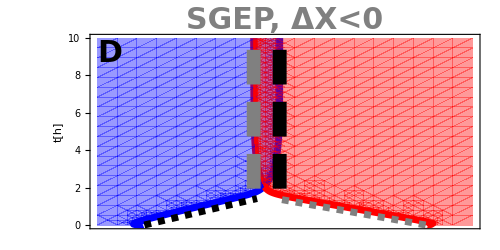

```mathematica
plotSGEP1=Show[{ContourPlot[Evaluate[{ϵ11*n1[x,t]+ϵ12*n2[x,t]==c1/.sol2,ϵ21*n1[x,t]+ϵ22*n2[x,t]==c2/.sol2}/.t->3600*τ],{x,-L/2,L/2},{τ,0,tmax/3600},ContourStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}},LabelStyle->{Bold,30},ContourLabels->None,FrameLabel->{None(*"x[μm]"*),"t[h]"},FrameTicks->{{Automatic,None},{None,None}},PlotRangeClipping->False,ImagePadding->{{Automatic,Automatic},{Automatic,50}},MaxRecursion->5,PerformanceGoal->"Quality",AspectRatio->1/2,Epilog->{
(*Inset[LineLegend[{Directive[{Blue,Thickness[0.01]}],Directive[{Red,Thickness[0.01]}],Directive[{Black,Dashed,Thickness[0.01]}],Directive[{Gray,Dashed,Thickness[0.01]}],Directive[{Black,Dashing[{0.05,0.025}],Thickness[0.02]}],Directive[{Gray,Dashing[{0.05,0.025}],Thickness[0.02]}]},{Style["X_1(t)",20,Bold],Style["X_2(t)",20,Bold],Style["X_1(0)+v_1t",20,Bold],Style["X_2(0)+v_2t",20,Bold],Style["vt-ΔX/2+c_0",20,Bold],Style["vt+ΔX/2+c_0",20,Bold]}],Scaled[{0.75,0.75}]],*)
Inset[Style["D",30,Bold],Scaled[{0.05,.9}]],Inset[Style["SGEP, ΔX<0",Bold,30,Gray],Scaled[{0.5,1.07}]]}
],
RegionPlot[Evaluate[{ϵ11*n1[x,t]+ϵ12*n2[x,t]>c1/.sol2,ϵ21*n1[x,t]+ϵ22*n2[x,t]>c2/.sol2}/.t->3600*τ],{x,-L/2,L/2},{τ,0,tmax/3600},BoundaryStyle->None,PlotStyle->{Directive[Blue,Opacity[0.4]],Directive[Red,Opacity[0.4]]},MaxRecursion->5,PerformanceGoal->"Quality"],ParametricPlot[Evaluate[{{HeavisideTheta[T0/3600-t]*(x1+v1*3600*t)+HeavisideTheta[t-T0/3600]*(center+v*(3600*t-tmax)-Δc/2),t},{HeavisideTheta[T0/3600-t]*(x2+v2*3600*t)+HeavisideTheta[t-T0/3600]*(center+v*(3600*t-tmax)+Δc/2),t}}/.solV],{t,0,T0/3600-0.1},(*RegionFunction->Function[{x,y,u,v},!((T0-100)<u)],*)PlotStyle->{{Black,Thickness[0.01],Dashed},{Gray,Thickness[0.01],Dashed}}],
ParametricPlot[Evaluate[{{center+v*(3600*t-tmax)-Δc/2,t},{center+v*(3600*t-tmax)+Δc/2,t}}/.solV],{t,7000/3600,tmax/3600},(*,PlotRange->{Automatic,{0,tmax}},*)PlotStyle->{{Black,Thickness[0.02],Dashing[{0.05,0.025}]},{Gray,Thickness[0.02],Dashing[{0.05,0.025}]}}]},ImageSize->{500,250}]
```

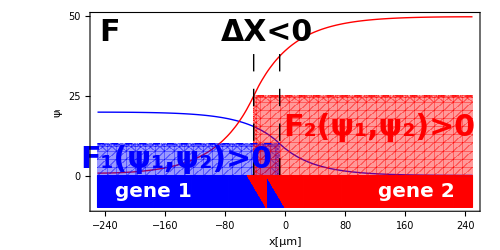

```mathematica
profile1=Show[Plot[Evaluate[{n1[x,tmax],n2[x,tmax](*n1[empX1,tmax]*UnitStep[empX1-x],n2[empX2,tmax]UnitStep[x-empX2]*)}/.sol2],{x,-L/2,L/2},FrameLabel->{"x[μm]","ψ_i"},PlotRange->{Automatic,{-10,50}},LabelStyle->{Bold,30,Gray},PlotStyle->{{Thick,Blue},{Red,Thick},{Blue,Dashed},{Red,Dashed}},Frame->True,FrameTicks->{{{0,25,50},None},{Automatic,None}},AspectRatio->0.5,ImageSize->{500,250},AxesOrigin->{-250,0},PlotRangeClipping->False,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}},Epilog->{Inset[Style["F_1(ψ_1,ψ_2)>0",Bold,30,Blue],{-145,5}],Inset[Style["F_2(ψ_1,ψ_2)>0",Bold,30,Red],{125,15}],Inset[Style["ΔX<0",30,Bold],{(empX1+empX2)/2,45}],Inset[Style["F",30,Bold],Scaled[{0.05,.9}]],{Dashing[0.025],Thick,Line[{{empX1,0},{empX1,42}}]},{Dashing[0.025],Thick,Line[{{empX2,0},{empX2,42}}]},{Dashed,Thick,Blue,Line[{{-L/2,n1[empX1,tmax]},{empX1,n1[empX1,tmax]}}/.sol2]},{Dashed,Thick,Red,Line[{{L/2,n2[empX2,tmax]},{empX2,n2[empX2,tmax]}}/.sol2]},
y0=-10;y1=0;
Table[{Blue,EdgeForm[Thick],Rectangle[{-250+i*25,y0},{-250+(i+1)*25,y1}]},{i,0,7}],
Table[{Blue,EdgeForm[Thick],Triangle[{{-250+i*25,y0},{-250+(i+1)*25,y0},{-250+i*25,y1}}]},{i,8,9}],
Table[{Red,EdgeForm[Thick],Triangle[{{-250+i*25,y1},{-250+(i+1)*25,y1},{-250+(i+1)*25,y0}}]},{i,8,9}],
Table[{Red,EdgeForm[Thick],Rectangle[{-250+i*25,y0},{-250+(i+1)*25,y1}]},{i,10,19}],
Inset[Style["gene 1",White,Bold,20],{-175 ,(y0+y1)/2}],Inset[Style["gene 2",White,Bold,20],{175 ,(y0+y1)/2}]
}
],
RegionPlot[Evaluate[{ψ<n1[empX1,tmax]&&x<empX1,ψ<n2[empX2,tmax]&&x>empX2}/.sol2],{x,-L/2,L/2},{ψ,0,100},BoundaryStyle->None,PlotStyle->{{Directive[Blue,Opacity[0.4]]},{Directive[Red,Opacity[0.4]]}},PlotPoints->40]]
```

```mathematica
tmax=36000;
L=500;
(*exemplary params for non-stable dynamics*)
ϵ11=1.0;ϵ22=1.0;d1=1;d2=1;γ1=0.0005;γ2=0.0004;h1=0.01;h2=0.02;c1=4.5;c2=7.5;
λ1=Sqrt[d1/γ1]
λ2=Sqrt[d2/γ2]
S1=2c1*γ1/h1/ϵ11
S2=2c2*γ2/h2/ϵ22
R1=-0.6;
ϵ12=(2c1-ϵ11*h1/γ1)/(R1+1)/(h2/γ2)
R2=Sign[R1]*Abs[1-(1-Abs[R1])^(λ2/λ1)]
ϵ21=(2c2-ϵ22*h2/γ2)/(R2+1)/(h1/γ1)
Sign[R1]*λ2*Log[1-Abs[R1]]
sol2=NDSolve[{
D[n1[x,t],t]==d1*D[n1[x,t],{x,2}]-γ1*n1[x,t]+h1*UnitStep[ϵ11*n1[x,t]+ϵ12*n2[x,t]-c1],
D[n2[x,t],t]==d2*D[n2[x,t],{x,2}]-γ2*n2[x,t]+h2*UnitStep[ϵ22*n2[x,t]+ϵ21*n1[x,t]-c2],
n1[x,0]==1.1c1/ϵ11*UnitStep[x1-x],n2[x,0]==1.1c2/ϵ22*UnitStep[x-x2],(D[n1[x,t],x]/.x->-L/2)==0,(D[n1[x,t],x]/.x->L/2)==0,(D[n2[x,t],x]/.x->-L/2)==0,(D[n2[x,t],x]/.x->L/2)==0},{n1,n2},{x,-L/2,L/2},{t,0,tmax},AccuracyGoal->3, Method->{"PDEDiscretization"->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->2^11},"DifferentiateBoundaryConditions"->True},"TimeIntegration"->"BDF"},MaxStepSize->Automatic,StartingStepSize->Automatic];
Plot3D[Evaluate[{n1[x,t],n2[x,t]}/.sol2],{x,-L/2,L/2},{t,0,tmax},PlotRange->All]
v1=Sqrt[4d1*γ1]*Abs[S1-1]/Sqrt[1-(S1-1)^2];
v2=Sqrt[4d2*γ2]*Abs[S2-1]/Sqrt[1-(S2-1)^2];
T0=(x2-x1)/(Abs[v2]+Abs[v1]);
If[S1>1,v1=-v1];
If[S2<1,v2=-v2];
If[v1>0&&v2<0,X0=(Abs[v1]*x2+Abs[v2]*x1)/(Abs[v1]+Abs[v2])];
solV=FindRoot[{c1==ϵ11*h1/2/γ1*(-v/Sqrt[4d1*γ1+v^2]+1)+ϵ12*h2/2/γ2*(1-Sign[Δc]+Exp[v*Δc/4/d2-Abs[Δc]*Sqrt[4d2*γ2+v^2]/2/d2]*(v/Sqrt[4d2*γ2+v^2]+Sign[Δc])),c2==ϵ21*h1/2/γ1*(1-Sign[Δc]-Exp[-v*Δc/4/d1-Abs[Δc]*Sqrt[4d1*γ1+v^2]/2/d1]*(v/Sqrt[4d1*γ1+v^2]-Sign[Δc]))+ϵ22*h2/2/γ2*(v/Sqrt[4d2*γ2+v^2]+1)},{{v,0(*RandomReal[{-0.5,0.5}]*)},{Δc,(*RandomReal[{-0.5,0.5}]*)-20}}]
empX1=FindRoot[ϵ11*n1[x1,tmax]+ϵ12*n2[x1,tmax]==c1/.sol2,{x1,X0},AccuracyGoal->3][[1,2]];
empX2=FindRoot[ϵ21*n1[x2,tmax]+ϵ22*n2[x2,tmax]==c2/.sol2,{x2,X0},AccuracyGoal->3][[1,2]];
center=(empX2+empX1)/2;
```

44.7214

50.

0.45

0.3

-0.55

-0.641004

-4.87471

45.8145

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

-Graphics3D-

{v→-4.08458×10^-18,Δc→45.8145}

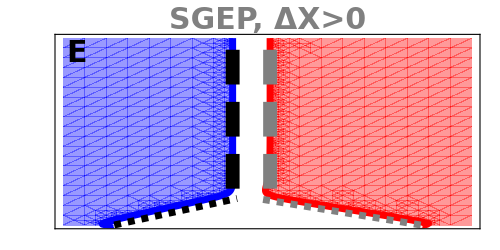

```mathematica
plotSGEP2=Show[{ContourPlot[Evaluate[{ϵ11*n1[x,t]+ϵ12*n2[x,t]==c1/.sol2,ϵ21*n1[x,t]+ϵ22*n2[x,t]==c2/.sol2}/.t->3600*τ],{x,-L/2,L/2},{τ,0,tmax/3600},ContourStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}},LabelStyle->{Bold,30},ContourLabels->None,FrameLabel->{None(*"x[μm]"*),None},FrameTicks->{{(*Table[{i,Style["a",Opacity[0]]},{i,0,10,0.5}]*)None,None},{None,None}},PlotRangeClipping->False,ImagePadding->{{Automatic,Automatic},{Automatic,50}},MaxRecursion->5,PerformanceGoal->"Quality",AspectRatio->1/2,Epilog->{
(*Inset[LineLegend[{Directive[{Blue,Thickness[0.01]}],Directive[{Red,Thickness[0.01]}],Directive[{Black,Dashed,Thickness[0.01]}],Directive[{Gray,Dashed,Thickness[0.01]}],Directive[{Black,Dashing[{0.05,0.025}],Thickness[0.02]}],Directive[{Gray,Dashing[{0.05,0.025}],Thickness[0.02]}]},{Style["X_1(t)",20,Bold],Style["X_2(t)",20,Bold],Style["X_1(0)+v_1t",20,Bold],Style["X_2(0)+v_2t",20,Bold],Style["vt-ΔX/2+c_0",20,Bold],Style["vt+ΔX/2+c_0",20,Bold]}],Scaled[{0.75,0.75}]],*)
Inset[Style["E",30,Bold],Scaled[{0.05,.9}]],Inset[Style["SGEP, ΔX>0",Bold,30,Gray],Scaled[{0.5,1.07}]]}
],
RegionPlot[Evaluate[{ϵ11*n1[x,t]+ϵ12*n2[x,t]>c1/.sol2,ϵ21*n1[x,t]+ϵ22*n2[x,t]>c2/.sol2}/.t->3600*τ],{x,-L/2,L/2},{τ,0,tmax/3600},BoundaryStyle->None,PlotStyle->{Directive[Blue,Opacity[0.4]],Directive[Red,Opacity[0.4]]},MaxRecursion->5,PerformanceGoal->"Quality",ImageSize->{500,500}],ParametricPlot[Evaluate[{{HeavisideTheta[T0/3600-t]*(x1+v1*3600*t)+HeavisideTheta[t-T0/3600]*(center+v*(3600*t-tmax)-Δc/2),t},{HeavisideTheta[T0/3600-t]*(x2+v2*3600*t)+HeavisideTheta[t-T0/3600]*(center+v*(3600*t-tmax)+Δc/2),t}}/.solV],{t,0,T0/3600-0.1},(*RegionFunction->Function[{x,y,u,v},!((T0-100)<u)],*)PlotStyle->{{Black,Thickness[0.01],Dashed},{Gray,Thickness[0.01],Dashed}}],
ParametricPlot[Evaluate[{{center+v*(3600*t-tmax)-Δc/2,t},{center+v*(3600*t-tmax)+Δc/2,t}}/.solV],{t,7000/3600,tmax/3600},(*,PlotRange->{Automatic,{0,tmax}},*)PlotStyle->{{Black,Thickness[0.02],Dashing[{0.05,0.025}]},{Gray,Thickness[0.02],Dashing[{0.05,0.025}]}}]},ImageSize->{500,250}]
```

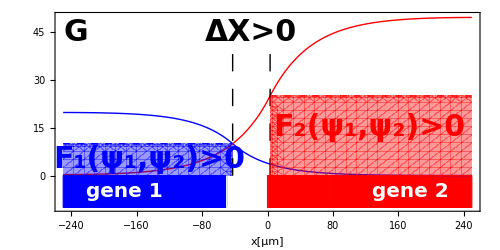

```mathematica
profile2=Show[Plot[Evaluate[{n1[x,tmax],n2[x,tmax](*n1[empX1,tmax]*UnitStep[empX1-x],n2[empX2,tmax]UnitStep[x-empX2]*)}/.sol2],{x,-L/2,L/2},FrameLabel->{"x[μm]",None(*"ψ_i"*)},LabelStyle->{Bold,30,Gray},PlotStyle->{{Thick,Blue},{Red,Thick},{Blue,Dashed},{Red,Dashed}},Filling->{3->Bottom,4->Bottom},Frame->True,FrameTicks->{{None,None},{Automatic,None}},FillingStyle->{{Directive[Blue,Opacity[0.7]]},{Directive[Red,Opacity[0.7]]}},AspectRatio->0.5,ImageSize->{500,250},AxesOrigin->{-250,0},PlotRangeClipping->False,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}},PlotRange->{Automatic,{-10,50}},Epilog->{Inset[Style["F_1(ψ_1,ψ_2)>0",Bold,30,Blue],{-145,5}],Inset[Style["F_2(ψ_1,ψ_2)>0",Bold,30,Red],{125,15}],Inset[Style["ΔX>0",30,Bold],{(empX1+empX2)/2,45}],Inset[Style["G",30,Bold],Scaled[{0.05,.9}]],{Dashing[0.025],Thick,Line[{{empX1,0},{empX1,42}}]},{Dashing[0.025],Thick,Line[{{empX2,0},{empX2,42}}]},{Dashed,Thick,Blue,Line[{{-L/2,n1[empX1,tmax]},{empX1,n1[empX1,tmax]}}/.sol2]},
Dashed,Thick,Red,Line[{{L/2,n2[empX2,tmax]},{empX2,n2[empX2,tmax]}}/.sol2],y0=-10;y1=0;
Table[{Blue,EdgeForm[Thick],Rectangle[{-250+i*25,y0},{-250+(i+1)*25,y1}]},{i,0,7}],
Table[{White,EdgeForm[Thick],Rectangle[{-250+i*25,y0},{-250+(i+1)*25,y1}]},{i,8,9}],
Table[{Red,EdgeForm[Thick],Rectangle[{-250+i*25,y0},{-250+(i+1)*25,y1}]},{i,10,19}],
Inset[Style["gene 1",White,Bold,20],{-175 ,(y0+y1)/2}],Inset[Style["gene 2",White,Bold,20],{175 ,(y0+y1)/2}]
}
],
RegionPlot[Evaluate[{ψ<n1[empX1,tmax]&&x<empX1,ψ<n2[empX2,tmax]&&x>empX2}/.sol2],{x,-L/2,L/2},{ψ,0,100},BoundaryStyle->None,PlotStyle->{{Directive[Blue,Opacity[0.4]]},{Directive[Red,Opacity[0.4]]}},PlotPoints->40]]
```

```mathematica
(*IGEP*)
tmax=36000;
L=500;
(*non-stable, overlapping*)
ϵ11=1.0;ϵ22=1.0;ϵ12=-0.21;ϵ21=-0.37;d1=1;d2=1;γ1=0.0005;γ2=0.0004;h1=0.01;h2=0.01;c1=3.5;c2=3.5;x1=-3L/8;x2=3L/8;
S1=2c1*γ1/h1/ϵ11
S2=2c2*γ2/h2/ϵ22
sol2=NDSolve[{
D[n1[x,t],t]==d1*D[n1[x,t],{x,2}]-γ1*n1[x,t]+h1*UnitStep[ϵ11*n1[x,t]+ϵ12*n2[x,t]-c1],
D[n2[x,t],t]==d2*D[n2[x,t],{x,2}]-γ2*n2[x,t]+h2*UnitStep[ϵ22*n2[x,t]+ϵ21*n1[x,t]-c2],
n1[x,0]==1.1c1/ϵ11*UnitStep[x1-x],n2[x,0]==1.1c2/ϵ22*UnitStep[x-x2],(D[n1[x,t],x]/.x->-L/2)==0,(D[n1[x,t],x]/.x->L/2)==0,(D[n2[x,t],x]/.x->-L/2)==0,(D[n2[x,t],x]/.x->L/2)==0},{n1,n2},{x,-L/2,L/2},{t,0,tmax},AccuracyGoal->3, Method->{"PDEDiscretization"->{"MethodOfLines","TemporalVariable"->t,"SpatialDiscretization"->{"TensorProductGrid","MinPoints"->2^11},"DifferentiateBoundaryConditions"->True},"TimeIntegration"->"BDF"},MaxStepSize->Automatic,StartingStepSize->Automatic];
Plot3D[Evaluate[{n1[x,t],n2[x,t]}/.sol2],{x,-L/2,L/2},{t,0,tmax},PlotRange->All]
v1=Sqrt[4d1*γ1]*Abs[S1-1]/Sqrt[1-(S1-1)^2];
v2=Sqrt[4d2*γ2]*Abs[S2-1]/Sqrt[1-(S2-1)^2];
T0=(x2-x1)/(Abs[v2]+Abs[v1]);
If[S1>1,v1=-v1];
If[S2<1,v2=-v2];
If[v1>0&&v2<0,X0=(Abs[v1]*x2+Abs[v2]*x1)/(Abs[v1]+Abs[v2])];
```

0.35

0.28

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

-Graphics3D-

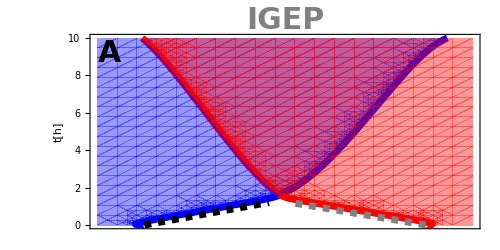

```mathematica
plotIGEP=Show[{ContourPlot[Evaluate[{ϵ11*n1[x,t]+ϵ12*n2[x,t]==c1/.sol2,ϵ21*n1[x,t]+ϵ22*n2[x,t]==c2/.sol2}/.t->3600*τ],{x,-L/2,L/2},{τ,0,tmax/3600},ContourStyle->{{Blue,Thickness[0.01]},{Red,Thickness[0.01]}},LabelStyle->{Bold,30},ContourLabels->None,FrameLabel->{None,"t[h]"},PlotRangeClipping->False,ImagePadding->{{Automatic,Automatic},{Automatic,50}},MaxRecursion->5,PerformanceGoal->"Quality",AspectRatio->1/2,FrameTicks->{{True,None},{None,None}},Epilog->{
(*Inset[LineLegend[{Directive[{Blue,Thickness[0.01]}],Directive[{Red,Thickness[0.01]}],Directive[{Black,Dashed,Thickness[0.01]}],Directive[{Gray,Dashed,Thickness[0.01]}],Directive[{Black,Dashing[{0.05,0.025}],Thickness[0.02]}],Directive[{Gray,Dashing[{0.05,0.025}],Thickness[0.02]}]},{Style["X_1(t)",20,Bold],Style["X_2(t)",20,Bold],Style["X_1(0)+v_1t",20,Bold],Style["X_2(0)+v_2t",20,Bold],Style["vt-ΔX/2+c_0",20,Bold],Style["vt+ΔX/2+c_0",20,Bold]}],Scaled[{0.75,0.75}]],*)
Inset[Style["A",30,Bold],Scaled[{0.05,.9}]],Inset[Style["IGEP",Bold,30,Gray],Scaled[{0.5,1.07}]]}
],
RegionPlot[Evaluate[{ϵ11*n1[x,t]+ϵ12*n2[x,t]>c1/.sol2,ϵ21*n1[x,t]+ϵ22*n2[x,t]>c2/.sol2}/.t->3600*τ],{x,-L/2,L/2},{τ,0,tmax/3600},BoundaryStyle->None,PlotStyle->{Directive[Blue,Opacity[0.4]],Directive[Red,Opacity[0.4]]},MaxRecursion->5,PerformanceGoal->"Quality"],ParametricPlot[{{HeavisideTheta[T0/3600-t]*(x1+v1*3600*t),t},{HeavisideTheta[T0/3600-t]*(x2+v2*3600*t),t}},{t,0,T0/3600-0.1},(*RegionFunction->Function[{x,y,u,v},!((T0-100)<u)],*)PlotStyle->{{Black,Thickness[0.01],Dashed},{Gray,Thickness[0.01],Dashed}}](*,
ParametricPlot[Evaluate[{{center+v*(3600*t-tmax)-Δc/2,t},{center+v*(3600*t-tmax)+Δc/2,t}}/.solV],{t,7000/3600,tmax/3600},(*,PlotRange->{Automatic,{0,tmax}},*)PlotStyle->{{Black,Thickness[0.02],Dashing[{0.05,0.025}]},{Gray,Thickness[0.02],Dashing[{0.05,0.025}]}}]*)},ImageSize->{500,250}]
```

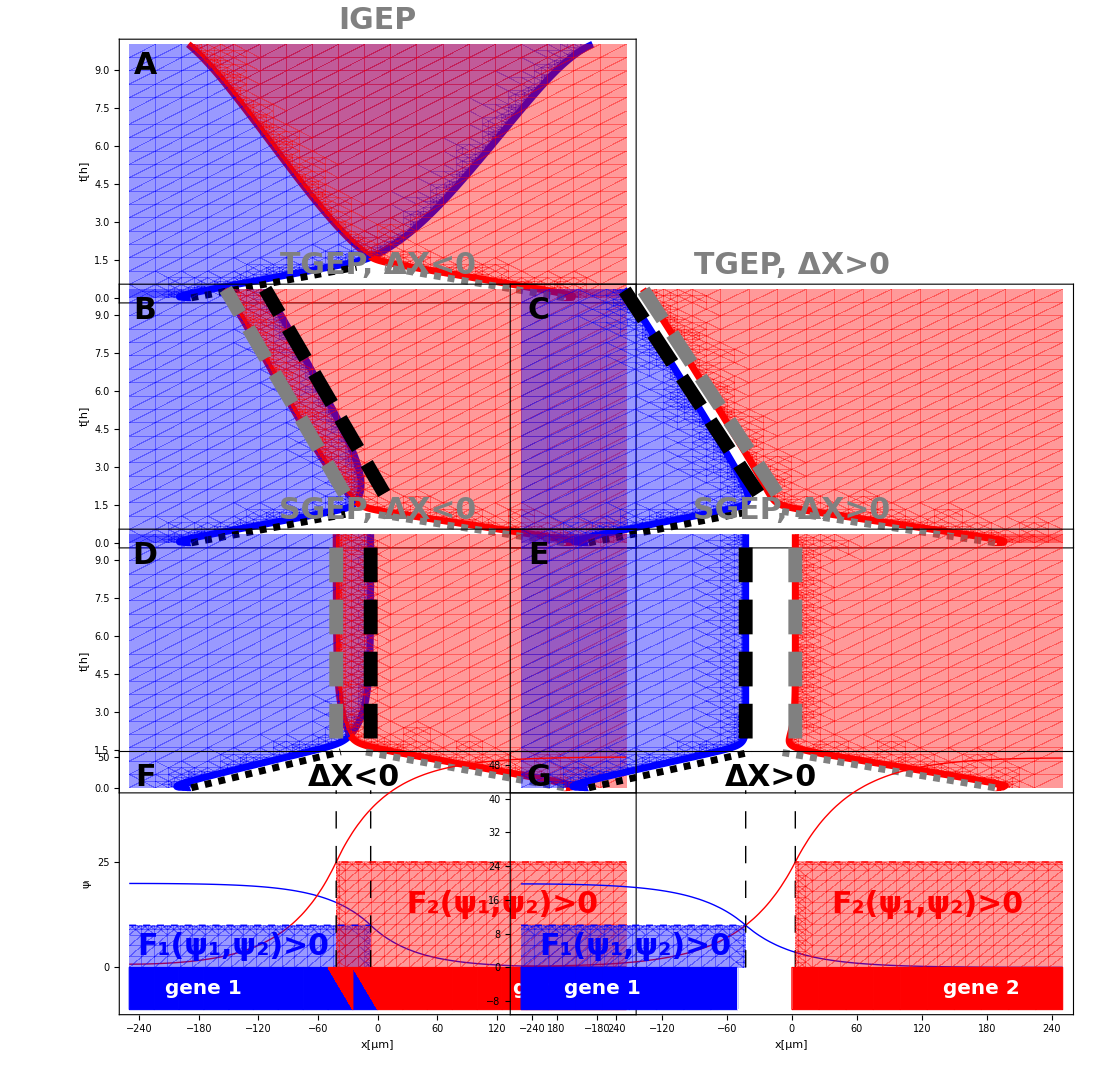

```mathematica
GraphicsGrid[{{plotIGEP,legend},{plotTGEP1,plotTGEP2},{plotSGEP1,plotSGEP2},{profile1,profile2}},ImageSize->{1100,Automatic},Spacings->{-170,-65},ImagePadding->{{290,290},{Automatic,Automatic}}]
```

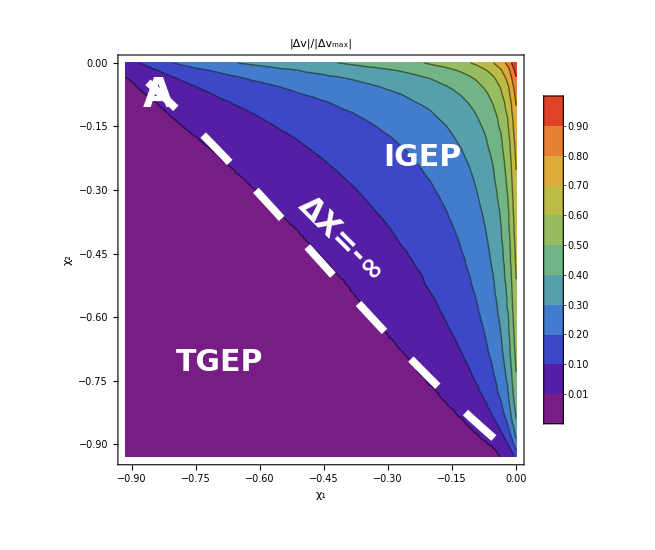

```mathematica
rawfronts=Uncompress[Import[NotebookDirectory[]<>"order parameter/fronts2500.dat"][[1,1]]];
rawfrontsdiag=Uncompress[Import[NotebookDirectory[]<>"order parameter/fronts_diag.dat"][[1,1]]];
rawfronts=Join[rawfronts,rawfrontsdiag];
L=5000;
trajlength[data_]:=Module[{tab=data,length=Length[data],n=10},While[(L/2-Abs[tab[[n,2]]]>=0.1L)&&(n<length),++n];Return[n]]
fronts=Table[{rawfronts[[i,1]],rawfronts[[i,2]],Take[rawfronts[[i,3]],trajlength[rawfronts[[i,3]]]],Take[rawfronts[[i,4]],trajlength[rawfronts[[i,4]]]]},{i,1,Length[rawfronts]}];
dataVfit=Table[{fronts[[i,1]],fronts[[i,2]],FindFit[Take[fronts[[i,3]],-Ceiling[Length[fronts[[i,3]]]/4]],v*t+c,{v,c},t,AccuracyGoal->5],FindFit[Take[fronts[[i,4]],-Ceiling[Length[fronts[[i,4]]]/4]],v*t+c,{v,c},t,AccuracyGoal->5]},{i,1,Length[fronts]}];
deltaVmax=Abs[dataVfit[[1,4,1,2]]-dataVfit[[1,3,1,2]]];
deltaV=Table[{dataVfit[[i,1]],dataVfit[[i,2]],Abs[dataVfit[[i,4,1,2]]-dataVfit[[i,3,1,2]]]/deltaVmax},{i,1,Length[dataVfit]}];
plotOrderParam=Show[ListContourPlot[deltaV,InterpolationOrder->1,ColorFunction->"Rainbow",PlotLegends->BarLegend[Automatic,LegendMarkerSize->430],PlotRange->{Automatic,Automatic,All},Contours->(*{0,-0.001,-0.005,-0.01,-0.015,-0.02}*)Table[If[i==0,0.01,0.1*i],{i,0,10}],PlotRangePadding->None,ContourLabels->None,FrameLabel->{"χ_1","χ_2"},PlotLabel->"|Δv|/|Δv_max|",LabelStyle->{30,Bold},(*RegionFunction->Function[{x,y,z},x>-0.4||x<-0.91||y>-0.6||y<-0.91],*)
Epilog->{Inset[Style["A",40,Bold,White],Scaled[{0.1,0.9}]],Inset[Rotate[Style["ΔX=-∞",30,Bold,White],-45Degree],Scaled[{0.55,0.55}]],Inset[Style["IGEP",30,Bold,White],Scaled[{0.75,0.75}]],Inset[Style["TGEP",30,Bold,White],Scaled[{0.25,0.25}]],
(*Inset[ListPointPlot3D[deltaV,PlotRange->All,ColorFunction->"Rainbow",Ticks->None,AxesLabel->{"χ_1","χ_2",(*"(|Δv|)/(|SubscriptBox[Δv, max]|)"*)"|Δv|/|Δv_max|"},LabelStyle->{20,Bold},AxesEdge->{{-1,-1},{1,-1},{-1,1}},ViewPoint->{0.95,-1.05,0.25},ImageSize->{400,200}],Scaled[{0.3,0.25}]]*)}
],
Plot[0.5(S2-1+If[(S1-1)/χ1-1>1,-1,1]/Sqrt[1+d2/d1*γ2/γ1*(1-(1-S1+2χ1)^2)/(1-S1+2χ1)^2])/.{d1->1,d2->1,γ1->0.0005,γ2->0.0004,S1->0.05,S2->0.1},{χ1,-1,0},PlotStyle->{White,Dashing[0.05,0.1],Thickness[0.01]}],ImageSize->{550,550}]
```

```mathematica
ListPointPlot3D[deltaV,PlotRange->All,ColorFunction->"Rainbow",Ticks->None,AxesLabel->{"χ_1","χ_2",(*"(|Δv|)/(|SubscriptBox[Δv, max]|)"*)"|Δv|/|Δv_max|"},LabelStyle->{20,Bold},AxesEdge->{{-1,-1},{1,-1},{-1,1}},ViewPoint->{0.95,-1.05,0.25},ImageSize->{600,400}]
```

-Graphics3D-

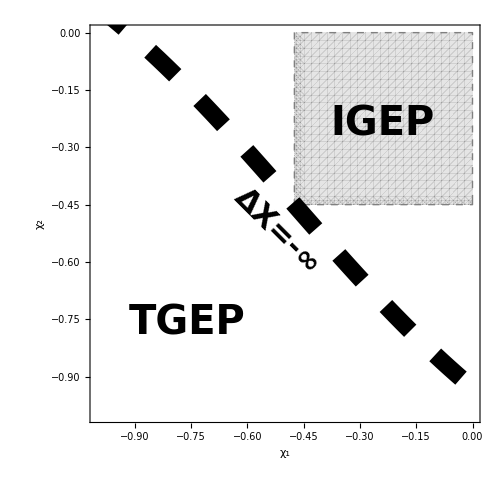

```mathematica
Show[RegionPlot[!((χ1<0&&χ2<S2-1)||((S1-1)/2>χ1&&S2/2>χ2>S2-1)||(S1/2>χ1>(S1-1)/2&&(S2-1)/2>χ2)||((S1-1)>χ1&&0>χ2))/.{S1->0.05,S2->0.1},{χ1,-1,0},{χ2,-1,0},PlotPoints->50,PlotStyle->{Gray,Opacity[0.2]},BoundaryStyle->{Gray,Thick,Dashed},FrameLabel->{"χ_1","χ_2"},LabelStyle->{20,Bold},ImageSize->{500,500}],Plot[0.5(S2-1+If[(S1-1)/χ1-1>1,-1,1]/Sqrt[1+d2/d1*γ2/γ1*(1-(1-S1+2χ1)^2)/(1-S1+2χ1)^2])/.{d1->1,d2->1,γ1->0.0005,γ2->0.0004,S1->0.05,S2->0.1},{χ1,-1,0},PlotStyle->{Thickness[0.025],Dashing[0.05,0.05],Black}],Epilog->{Inset[Style["TGEP",Bold,40],Scaled[{0.25,0.25}]],Inset[Style["IGEP",Bold,40],Scaled[{0.75,0.75}]],Inset[Rotate[Style["ΔX=-∞",30,Bold,Black],-45Degree],Scaled[{0.48,0.48}]]}]
```

```mathematica
d1=1;d2=1;γ1=0.0005;γ2=0.0004;S1=0.05;S2=0.1;
r=d2*γ2/(d1*γ1);
(*v->v/Sqrt[4d1γ1], Δc->Δc*Sqrt[4d1γ1]*)
plotχ=Flatten[ParallelTable[{χ1,χ2,
Quiet[FindRoot[{S1==(-v/Sqrt[1+v^2]+1)+χ1(1-Sign[Δc]+Exp[v*Δc/2/d2*(1-Sign[Δc]*Sqrt[r+v^2]/v)]*(v/Sqrt[r+v^2]+Sign[Δc])),S2==χ2(1-Sign[Δc]-Exp[-v*Δc/2/d1*(1+Sign[Δc]*Sqrt[1+v^2]/v)]*(v/Sqrt[1+v^2]-Sign[Δc]))+(v/Sqrt[r+v^2]+1)},{{v,RandomReal[{-10,10}]},{Δc,0(*RandomReal[{-100,100}]*)}},PrecisionGoal->4,MaxIterations->200]]},{χ1,-2,0,0.02},{χ2,-2,0,0.02}],1];
dataV=Table[{plotχ[[i,1]],plotχ[[i,2]],plotχ[[i,3,1,2]]*Sqrt[4*d1*γ1]*3600},{i,1,Length[plotχ]}];
dataΔX=Table[{plotχ[[i,1]],plotχ[[i,2]],plotχ[[i,3,2,2]]/Sqrt[4*d1*γ1]},{i,1,Length[plotχ]}];
```

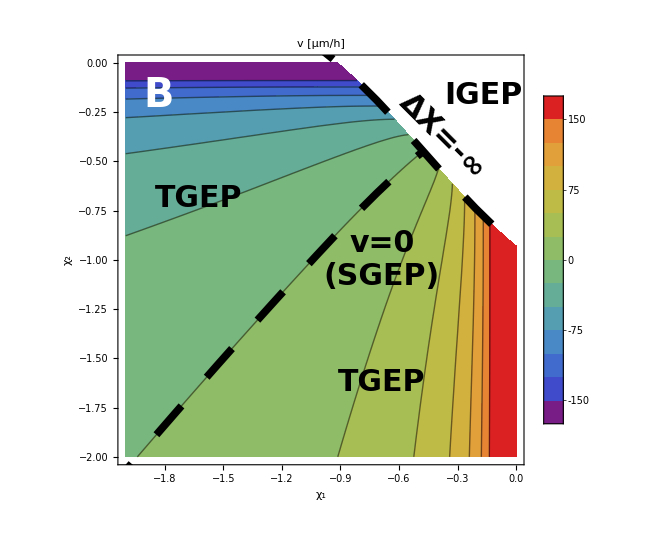

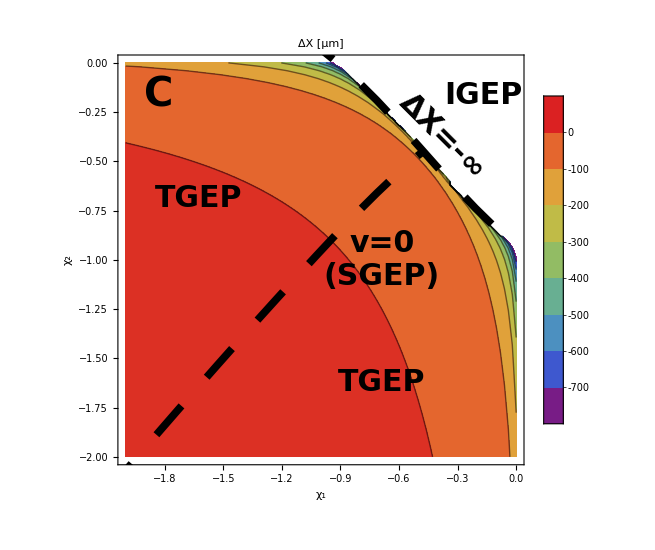

```mathematica
plotV=Show[
ListContourPlot[dataV,PlotRange->{{-2,0},{-2,0},{-200,200}},Axes->True,InterpolationOrder->1,PlotLegends->BarLegend[Automatic,LegendMarkerSize->430],Contours->Table[i,{i,-150,150,25}],ColorFunction->"Rainbow",ClippingStyle->{ColorData["Rainbow"][0],ColorData["Rainbow"][1]}(*Function[{z},If[z>ϵ,If[z<1-ϵ,ColorData["Rainbow"][(z-ϵ)/(1-2ϵ)],ColorData["Rainbow"][1]],ColorData["Rainbow"][0]]/.ϵ->0.2]*),ColorFunctionScaling->True,PlotRangePadding->None,ContourLabels->False,FrameLabel->{"χ_1","χ_2"},PlotLabel->"v [μm/h]",LabelStyle->{30,Bold},PlotRangePadding->None,RegionFunction->Function[{x,y,z},y<0.5(S2-1+If[(S1-1)/x-1>1,-1,1]/Sqrt[1+d2/d1*γ2/γ1*(1-(1-S1+2x)^2)/(1-S1+2x)^2])],Epilog->{Inset[Style["v=0\n(SGEP)",Bold,30],Scaled[{0.65,0.5}]],Inset[Rotate[Style["ΔX=-∞",Black,Bold,30],-45Degree],Scaled[{0.8,0.8}]](*,Inset[Style["S_1/2<χ_1\nS_2/2<χ_2",Bold,20,Gray],Scaled[{0.89,0.89}]]*),Inset[Style["TGEP",30,Bold],Scaled[{0.2,0.65}]],Inset[Style["TGEP",30,Bold],Scaled[{0.65,0.2}]],Inset[Style["IGEP",30,Bold],Scaled[{0.9,0.9}]],Inset[Style["B",40,White,Bold],Scaled[{0.1,0.9}]]}],
(*RegionPlot[!((χ1<0&&χ2<S2-1)||((S1-1)/2>χ1&&S2/2>χ2>S2-1)||(S1/2>χ1>(S1-1)/2&&(S2-1)/2>χ2)||((S1-1)>χ1&&0>χ2)),{χ1,-2,0},{χ2,-2,0},PlotPoints->50,PlotStyle->{Gray,Opacity[0.2]},BoundaryStyle->{Gray,Dashed}],*)
Plot[{(S2-1)/(1+Sign[R](1-(1-Abs[R])^Sqrt[d2*γ1/d1/γ2]))/.{R->(S1-1)/χ1-1},0.5(S2-1+If[(S1-1)/χ1-1>1,-1,1]/Sqrt[1+d2/d1*γ2/γ1*(1-(1-S1+2χ1)^2)/(1-S1+2χ1)^2])},{χ1,-5,0},PlotStyle->{{Black,Dashing[0.05,0.1],Thickness[0.01]},{Black,Dashing[0.05,0.1],Thickness[0.01]}}],ImageSize->{550,550}]
plotDeltaX=Show[
ListContourPlot[dataΔX,PlotRange->{{-2,0},{-2,0},{-800,100}},ColorFunction->"Rainbow",InterpolationOrder->1,PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->430],Automatic],ContourLabels->False,FrameLabel->{"χ_1","χ_2"},PlotLabel->"ΔX [μm]",LabelStyle->{30,Bold},PlotRangePadding->None,RegionFunction->Function[{x,y,z},y<0.5(S2-1+If[(S1-1)/x-1>1,-1,1]/Sqrt[1+d2/d1*γ2/γ1*(1-(1-S1+2x)^2)/(1-S1+2x)^2])],Epilog->{Inset[Style["v=0\n(SGEP)",Bold,30],Scaled[{0.65,0.5}]],Inset[Rotate[Style["ΔX=-∞",Black,Bold,30],-45Degree],Scaled[{0.8,0.8}]](*,Inset[Style["S_1/2<χ_1\nS_2/2<χ_2",Bold,20,Gray],Scaled[{0.89,0.89}]]*),Inset[Style["TGEP",30,Bold],Scaled[{0.2,0.65}]],Inset[Style["TGEP",30,Bold],Scaled[{0.65,0.2}]],Inset[Style["IGEP",30,Bold],Scaled[{0.9,0.9}]],Inset[Style["C",40,Bold],Scaled[{0.1,0.9}]]}],
(*RegionPlot[!((χ1<0&&χ2<S2-1)||((S1-1)/2>χ1&&S2/2>χ2>S2-1)||(S1/2>χ1>(S1-1)/2&&(S2-1)/2>χ2)||((S1-1)>χ1&&0>χ2)),{χ1,-2,0},{χ2,-2,0},PlotPoints->50,PlotStyle->{Gray,Opacity[0.2]},BoundaryStyle->{Gray,Dashed}],*)
Plot[{(S2-1)/(1+Sign[R](1-(1-Abs[R])^Sqrt[d2*γ1/d1/γ2]))/.{R->(S1-1)/χ1-1},0.5(S2-1+If[(S1-1)/χ1-1>1,-1,1]/Sqrt[1+d2/d1*γ2/γ1*(1-(1-S1+2χ1)^2)/(1-S1+2χ1)^2])},{χ1,-5,0},PlotStyle->{{Black,Dashing[0.05,0.1],Thickness[0.01]},{Black,Dashing[0.05,0.1],Thickness[0.01]}}],ImageSize->{550,550}]
```

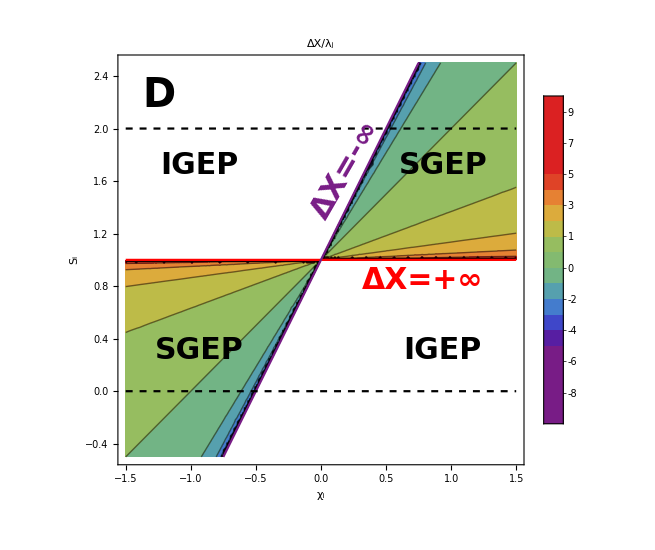

```mathematica
plotSGEP=Show[ContourPlot[Sign[R]*Log[1-Abs[R]]/.R->(s-1)/x-1,{x,-1.5,1.5},{s,-0.5,2.5},PlotRange->{Automatic,Automatic,{-10,10}},Contours->Table[If[i==0,0,i-10],{i,0,20,1}],(*PlotPoints->100,*)ColorFunction->Function[{z},If[z>ϵ,If[z<1-ϵ,ColorData["Rainbow"][(z-ϵ)/(1-2ϵ)],ColorData["Rainbow"][1]],ColorData["Rainbow"][0]]/.ϵ->0.25],ColorFunctionScaling->True,Axes->True,FrameLabel->{"χ_i","S_i"},PlotLabel->"ΔX/λ_j ",LabelStyle->{Bold,30},PlotLegends->BarLegend[Automatic,LegendMarkerSize->430],PlotRangePadding->None,ContourLabels->None,
Epilog->{Inset[Style["ΔX=+∞",Red,30,Bold],Scaled[{0.75,0.45}]],(*Inset[Style["ΔX=0",Gray,30,Bold],Scaled[{0.68,0.6}]],*)Inset[Rotate[Style["ΔX=-∞",ColorData["Rainbow"][0],30,Bold],60Degree],Scaled[{0.56,0.72}]],Inset[Style["IGEP",30,Bold],Scaled[{0.8,0.28}]],Inset[Style["IGEP",30,Bold],Scaled[{0.2,0.73}]],Inset[Style["SGEP",30,Bold],Scaled[{0.2,0.28}]],Inset[Style["SGEP",30,Bold],Scaled[{0.8,0.73}]],Inset[Style["D",Bold,40],Scaled[{0.1,0.9}]]}
],
Plot[{1,(*x+1,*)2x+1},{x,-1.5,1.5},PlotRange->{Automatic,{-0.5,2.5}},PlotStyle->{{Red},(*{Gray},*){ColorData["Rainbow"][0]}}],Plot[{0,2},{x,-1.5,1.5},PlotRange->{Automatic,{-0.5,2.5}},PlotStyle->{{Dashed,Black},{Dashed,Black}}(*,Filling->{1->Bottom,2->Top}*)],ImageSize->{550,550},ImageMargins->Automatic]
```

```mathematica
GraphicsGrid[{{plotOrderParam,plotV},{plotDeltaX,plotSGEP}},ImageSize->{1350,1200},Spacings->{-50,-25}]
Export[NotebookDirectory[]<>"fig3all.png",GraphicsGrid[{{plotOrderParam,plotV},{plotDeltaX,plotSGEP}},ImageSize->{1350,1200},Spacings->{-50,-25}]];
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"data/05_07.dat",Compress[plotχ]];
```

```mathematica
test=Uncompress[Import[NotebookDirectory[]<>"data/05_07.dat"][[1,1]]];
```

```mathematica
test[[2]]
```

{-4.,-3.99,{v→0.00110051,Δc→109.314}}

```mathematica
Manipulate[Plot[{Sign[x](Exp[-Abs[x]]),a+Sign[x]},{x,-10,10}],{a,-2,2}]
```

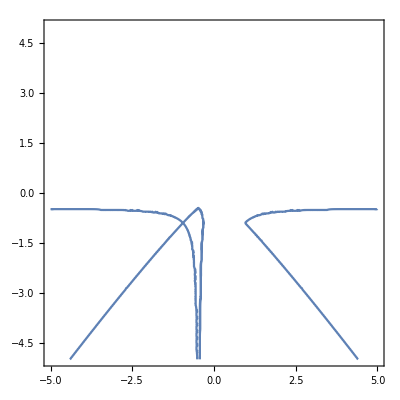

```mathematica
ContourPlot[Evaluate[(1-Abs[R1])^λ2==(1-Abs[R2])^λ1/.{λ1->Sqrt[d1/γ1],λ2->Sqrt[d2/γ2],R1->(S1-1)/χ1-1,R2->(S2-1)/χ2-1}],{χ1,-5,5},{χ2,-5,5},PlotPoints->50]
```

```mathematica
Manipulate[Show[
RegionPlot[{
χ1<0&&χ2<S2-1,
(S1-1)/2>χ1&&S2/2>χ2>S2-1,
S1/2>χ1>(S1-1)/2&&(S2-1)/2>χ2,
(S1-1)>χ1&&0>χ2},{χ1,-2,0},{χ2,-2,0},FrameLabel->{"χ1","χ2"}],
Plot[{(S2-1)/(1+Sign[R](1-(1-Abs[R])^1.5))/.{R->(S1-1)/χ1-1},-1/χ1},{χ1,-5,0},PlotStyle->Black],
ContourPlot[(1-S1+2χ1)^2/(1-(1-S1+2χ1)^2)==(1-S1+2χ2)^2/(1-(1-S2+2χ2)^2),{χ1,-2,0},{χ2,-2,0},PlotPoints->50]
],
{S1,0,1},{S2,0,1}]
```

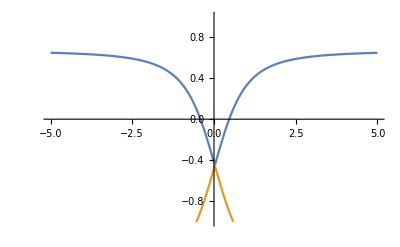

```mathematica
d1=1;d2=1;γ1=0.0005;γ2=0.0004;S1=1.05;S2=0.1;
Plot[{0.5(S2-1+If[(S1-1)/χ1-1>1,-1,1]/Sqrt[1+d2/d1*γ2/γ1*(1-(1-S1+2χ1)^2)/(1-S1+2χ1)^2]),0.5(S2-1+If[(S1-1)/χ1-1>1,1,-1]/Sqrt[1+d2/d1*γ2/γ1*(1-(1-S1+2χ1)^2)/(1-S1+2χ1)^2])},{χ1,-5,5},PlotRange->{Automatic,{-1,1}}]
```

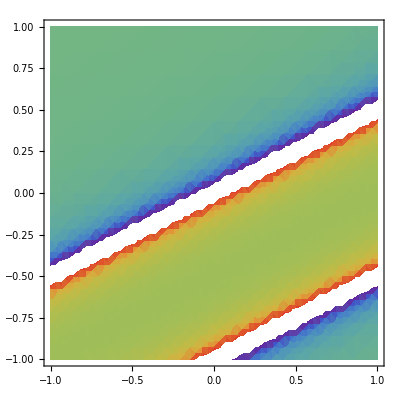

```mathematica
DensityPlot[(1-S+2χ)^2/(1-(1-S+2χ)^2),{S,-1,1},{χ,-1,1},PlotRange->Automatic,ColorFunction->"Rainbow"]
```

```mathematica
Manipulate[ContourPlot[{S==1+2χ-V,S==1+2χ+V,S-1==V,S-1==-V},{χ,-2,3},{S,-3,3},ContourStyle->Table[{Dashed, Black},4]],{V,0,1}]
```

```mathematica
Manipulate[Show[RegionPlot[{1>(S-1+V)/(χ(V+1))>0,1>(S-1+V-2χ)/(χ(V-1))>0},{χ,-2,2},{S,-1,3},PlotPoints->40],ContourPlot[{S==1+2χ-V,S==1+2χ+V,S-1==V,S-1==-V},{χ,-2,3},{S,-3,3},ContourStyle->Table[{Dashed, Black},4]]],{V,-1,1}]
```

Power::infy: Infinite expression 1/0 encountered.

Greater::nord: Invalid comparison with ComplexInfinity attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

```mathematica
plotregion=Show[RegionPlot[{
2x+1>s&&s>1,
s<0&&s>2x+1,
0<s<1&&s>2x+1,
1>s>0&&s>2+2x,
2x+1>s&&s>2,
s<0&&s>2+2x
},{x,-2,2},{s,-1,3},PlotPoints->50,PlotStyle->{Directive[RGBColor[0.75,0.1,0.1],Opacity[1]],Directive[RGBColor[0.1,0.5,0.1],Opacity[1]],Directive[RGBColor[0.1,0.1,0.95],Opacity[1]],{HatchFilling[63.26Degree,2],White},{HatchFilling[90Degree,2],White},{HatchFilling[0Degree,2],White}},BoundaryStyle->None,FrameLabel->{"χ_i","S_i"},LabelStyle->{30,Bold},Axes->True,PlotRangeClipping->False,PlotRangePadding->None,ImagePadding->{{Automatic,Automatic},{Automatic,50}}],
Plot[{0,1,2},{x,-2,2},PlotStyle->Table[{Dashed,Thick,Black},3]],
(*Plot[Table[2x-δ,{δ,-1,2,0.1}],{x,0.5,2},PlotRange->{Automatic,{2,3}},PlotStyle->{Orange,Dashed}],
Plot[Table[2x-δ,{δ,-5,-2,0.1}],{x,-3,-0.5},PlotRange->{Automatic,{0,1}},PlotStyle->{White,Dashed}],
Plot[Table[2x-δ,{δ,-5,-2,0.1}],{x,-3,-0.5},PlotRange->{Automatic,{-1,0}},PlotStyle->{RGBColor[0.15,0.15,0.15],Dashed},RegionFunction->Function[{x,y},x>-2]],*)
ImageSize->{600,600},Epilog->{
Inset[Style["(ϵ_ii,ϵ_ij,C_i)",30,Gray,Bold],Scaled[{0.5,1.05}]],
Inset[Style["(+,+,+)",White,30,Bold],{1.5,1.5}],
Inset[Rotate[Style["(+,-,+)",White,30,Bold],60Degree],{-0.5,0.5}],
Inset[Rotate[Style["(+,-,-)",White,30,Bold],60Degree],{-1,-0.5}],
Inset[Rotate[Style["(-,+,+)",White,30,Bold],60Degree],{-1.65,-0.5}],
Inset[Style["(-,+,-)",White,30,Bold],{-1.5,0.5}],
Inset[Style["(-,-,-)",White,30,Bold],{1.5,2.5}],
Inset[Style["(-,-,+)",Black,30,Bold],{0.4,-0.3}],
Inset[Style["(+,+,-)",Black,30,Bold],{0.4,-0.6}],
Inset[Style["collapse",30,Bold,Gray],{-1.4,2.5}],
Inset[Style["shrinking",30,Bold,Gray],{-1.35,1.5}],
Inset[Style["expansion",30,Bold,Gray],{1.35,0.5}],
Inset[Style["collapse",30,Bold,Gray],{1.4,-0.5}]}
(*,Prolog->Inset[Image[Import[NotebookDirectory[]<>"halfmotif.png"],ImageSize->250],{-0.75,2.25}]*)
]
```

-Graphics-

```mathematica
motifs=Plot[,{x,-1,1},AspectRatio->1,Axes->False,ImageSize->{600,600}];
GraphicsRow[{plotregion,motifs},ImageSize->{1100,Automatic},Spacings->{-60,Automatic},Epilog->{
Inset[Image[Import[NotebookDirectory[]<>"interaction_charts/minus_minus.png"],ImageSize->240],Scaled[{0.625,0.7}]],Inset[Image[Import[NotebookDirectory[]<>"interaction_charts/minus_plus.png"],ImageSize->240],Scaled[{0.875,0.7}]],
Inset[Image[Import[NotebookDirectory[]<>"interaction_charts/plus_minus.png"],ImageSize->240],Scaled[{0.625,0.3}]],Inset[Image[Import[NotebookDirectory[]<>"interaction_charts/plus_plus.png"],ImageSize->240],Scaled[{0.875,0.3}]],
Inset[Style["(-,-,±)",40,Bold],Scaled[{0.625,0.85}]],Inset[Style["(-,+,±)",40,Bold],Scaled[{0.875,0.85}]],Inset[Style["(+,-,±)",40,Bold],Scaled[{0.625,0.45}]],Inset[Style["(+,+,±)",40,Bold],Scaled[{0.875,0.45}]]
}]
```

-Graphics-